# Expression of scattering amplitudes in QH setup

```mathematica
Clear["Global`*"]
P=Solve[{b1==r1*a1+I*t1*x1,y1==I*t1*a1+r1*x1,b2==r2*a2+I*t2*x2,y2==I*t2*a2+r2*x2,b3==r3*a3+I*t3*x3,y3==I*t3*a3+r3*x3,b4==r4*a4+I*t4*x4,y4==I*t4*a4+r4*x4,x1==y4,x3==q*y1+p*y2,x2==p*y1+q*y2,y3==x4},{b1,b2,b3,b4,y1,y2,y3,y4,x1,x2,x3,x4}];
b1=b1/.P[[1]];
b2=b2/.P[[1]];
b3=b3/.P[[1]];
b4=b4/.P[[1]];
s11=b1/.{a1->1,a2->0,a3->0,a4->0}//FullSimplify
s12=b1/.{a1->0,a2->1,a3->0,a4->0}//FullSimplify
s13=b1/.{a1->0,a2->0,a3->1,a4->0}//FullSimplify
s14=b1/.{a1->0,a2->0,a3->0,a4->1}//FullSimplify
s21=b2/.{a1->1,a2->0,a3->0,a4->0}//FullSimplify
s22=b2/.{a1->0,a2->1,a3->0,a4->0}//FullSimplify
s23=b2/.{a1->0,a2->0,a3->1,a4->0}//FullSimplify
s24=b2/.{a1->0,a2->0,a3->0,a4->1}//FullSimplify
s31=b3/.{a1->1,a2->0,a3->0,a4->0}//FullSimplify
s32=b3/.{a1->0,a2->1,a3->0,a4->0}//FullSimplify
s33=b3/.{a1->0,a2->0,a3->1,a4->0}//FullSimplify
s34=b3/.{a1->0,a2->0,a3->0,a4->1}//FullSimplify
s41=b4/.{a1->1,a2->0,a3->0,a4->0}//FullSimplify
s42=b4/.{a1->0,a2->1,a3->0,a4->0}//FullSimplify
s43=b4/.{a1->0,a2->0,a3->1,a4->0}//FullSimplify
s44=b4/.{a1->0,a2->0,a3->0,a4->1}//FullSimplify
```

r1+((q+p^2 r2-q^2 r2) r3 r4 t1^2)/(-1+q r2+r1 (q+p^2 r2-q^2 r2) r3 r4)

(p r3 r4 t1 t2)/(-1+q r2+r1 (q+p^2 r2-q^2 r2) r3 r4)

((-1+q r2) r4 t1 t3)/(1-q r2-r1 (q+p^2 r2-q^2 r2) r3 r4)

((-1+q r2) t1 t4)/(1-q r2-r1 (q+p^2 r2-q^2 r2) r3 r4)

(p t1 t2)/(-1+q r2+r1 (q+p^2 r2-q^2 r2) r3 r4)

r2+((q+p^2 r1 r3 r4-q^2 r1 r3 r4) t2^2)/(-1+q r2+r1 (q+p^2 r2-q^2 r2) r3 r4)

(p r1 r4 t2 t3)/(-1+q r2+r1 (q+p^2 r2-q^2 r2) r3 r4)

(p r1 t2 t4)/(-1+q r2+r1 (q+p^2 r2-q^2 r2) r3 r4)

((q+p^2 r2-q^2 r2) t1 t3)/(-1+q r2+r1 (q+p^2 r2-q^2 r2) r3 r4)

(p t2 t3)/(-1+q r2+r1 (q+p^2 r2-q^2 r2) r3 r4)

r3+(r1 (q+p^2 r2-q^2 r2) r4 t3^2)/(-1+q r2+r1 (q+p^2 r2-q^2 r2) r3 r4)

(r1 (q+p^2 r2-q^2 r2) t3 t4)/(-1+q r2+r1 (q+p^2 r2-q^2 r2) r3 r4)

((q+p^2 r2-q^2 r2) r3 t1 t4)/(-1+q r2+r1 (q+p^2 r2-q^2 r2) r3 r4)

(p r3 t2 t4)/(-1+q r2+r1 (q+p^2 r2-q^2 r2) r3 r4)

((-1+q r2) t3 t4)/(1-q r2-r1 (q+p^2 r2-q^2 r2) r3 r4)

r4+(r1 (q+p^2 r2-q^2 r2) r3 t4^2)/(-1+q r2+r1 (q+p^2 r2-q^2 r2) r3 r4)

# Expression of scattering amplitudes in QSH setup

```mathematica
Clear["Global`*"]
P=Solve[{b1u==r1*a1u+I*t1*x1u,y1u==I*t1*a1u+r1*x1u,b2u==r2*a2u+I*t2*x2u,y2u==I*t2*a2u+r2*x2u,b3u==r3*a3u+I*t3*x3u,y3u==I*t3*a3u+r3*x3u,b4u==r4*a4u+I*t4*x4u,y4u==I*t4*a4u+r4*x4u,x1u==y4u,x3u==q*y1u+p*y2u,x2u==p*y1u+q*y2u,y3u==x4u,(*d sector*)b1d==r1*a1d+I*t1*x1d,y1d==I*t1*a1d+r1*x1d,b2d==r2*a2d+I*t2*x2d,y2d==I*t2*a2d+r2*x2d,b3d==r3*a3d+I*t3*x3d,y3d==I*t3*a3d+r3*x3d,b4d==r4*a4d+I*t4*x4d,y4d==I*t4*a4d+r4*x4d,x1d==q*y3d+p*y2d,x4d==y1d,x2d==p*y3d+q*y2d,y4d==x3d},{b1u,b2u,b3u,b4u,y1u,y2u,y3u,y4u,x1u,x2u,x3u,x4u,b1d,b2d,b3d,b4d,y1d,y2d,y3d,y4d,x1d,x2d,x3d,x4d}];
b1u=b1u/.P[[1]];
b2u=b2u/.P[[1]];
b3u=b3u/.P[[1]];
b4u=b4u/.P[[1]];
b1d=b1d/.P[[1]];
b2d=b2d/.P[[1]];
b3d=b3d/.P[[1]];
b4d=b4d/.P[[1]];
s11uu=b1u/.{a1u->1,a2u->0,a3u->0,a4u->0}//FullSimplify;
s12uu=b1u/.{a1u->0,a2u->1,a3u->0,a4u->0}//FullSimplify;
s13uu=b1u/.{a1u->0,a2u->0,a3u->1,a4u->0}//FullSimplify;
s14uu=b1u/.{a1u->0,a2u->0,a3u->0,a4u->1}//FullSimplify;
s21uu=b2u/.{a1u->1,a2u->0,a3u->0,a4u->0}//FullSimplify;
s22uu=b2u/.{a1u->0,a2u->1,a3u->0,a4u->0}//FullSimplify;
s23uu=b2u/.{a1u->0,a2u->0,a3u->1,a4u->0}//FullSimplify;
s24uu=b2u/.{a1u->0,a2u->0,a3u->0,a4u->1}//FullSimplify;
s31uu=b3u/.{a1u->1,a2u->0,a3u->0,a4u->0}//FullSimplify;
s32uu=b3u/.{a1u->0,a2u->1,a3u->0,a4u->0}//FullSimplify;
s33uu=b3u/.{a1u->0,a2u->0,a3u->1,a4u->0}//FullSimplify;
s34uu=b3u/.{a1u->0,a2u->0,a3u->0,a4u->1}//FullSimplify;
s41uu=b4u/.{a1u->1,a2u->0,a3u->0,a4u->0}//FullSimplify;
s42uu=b4u/.{a1u->0,a2u->1,a3u->0,a4u->0}//FullSimplify;
s43uu=b4u/.{a1u->0,a2u->0,a3u->1,a4u->0}//FullSimplify;
s44uu=b4u/.{a1u->0,a2u->0,a3u->0,a4u->1}//FullSimplify;
s11dd=b1d/. {a1d->1,a2d->0,a3d->0,a4d->0}//FullSimplify
s12dd=b1d/. {a1d->0,a2d->1,a3d->0,a4d->0}//FullSimplify
s13dd=b1d/. {a1d->0,a2d->0,a3d->1,a4d->0}//FullSimplify
s14dd=b1d/. {a1d->0,a2d->0,a3d->0,a4d->1}//FullSimplify
s21dd=b2d/. {a1d->1,a2d->0,a3d->0,a4d->0}//FullSimplify
s22dd=b2d/. {a1d->0,a2d->1,a3d->0,a4d->0}//FullSimplify
s23dd=b2d/. {a1d->0,a2d->0,a3d->1,a4d->0}//FullSimplify
s24dd=b2d/. {a1d->0,a2d->0,a3d->0,a4d->1}//FullSimplify
s31dd=b3d/. {a1d->1,a2d->0,a3d->0,a4d->0}//FullSimplify
s32dd=b3d/. {a1d->0,a2d->1,a3d->0,a4d->0}//FullSimplify
s33dd=b3d/. {a1d->0,a2d->0,a3d->1,a4d->0}//FullSimplify
s34dd=b3d/. {a1d->0,a2d->0,a3d->0,a4d->1}//FullSimplify
s41dd=b4d/. {a1d->1,a2d->0,a3d->0,a4d->0}//FullSimplify
s42dd=b4d/. {a1d->0,a2d->1,a3d->0,a4d->0}//FullSimplify
s43dd=b4d/. {a1d->0,a2d->0,a3d->1,a4d->0}//FullSimplify
s44dd=b4d/. {a1d->0,a2d->0,a3d->0,a4d->1}//FullSimplify
```

r1+((q+p^2 r2-q^2 r2) r3 r4 t1^2)/(-1+q r2+r1 (q+p^2 r2-q^2 r2) r3 r4)

(p t1 t2)/(-1+q r2+r1 (q+p^2 r2-q^2 r2) r3 r4)

((q+p^2 r2-q^2 r2) t1 t3)/(-1+q r2+r1 (q+p^2 r2-q^2 r2) r3 r4)

((q+p^2 r2-q^2 r2) r3 t1 t4)/(-1+q r2+r1 (q+p^2 r2-q^2 r2) r3 r4)

(p r3 r4 t1 t2)/(-1+q r2+r1 (q+p^2 r2-q^2 r2) r3 r4)

(r2^2+t2^2+((1-q r1 r3 r4) t2^2)/(-1+q r2+r1 (q+p^2 r2-q^2 r2) r3 r4))/r2

(p t2 t3)/(-1+q r2+r1 (q+p^2 r2-q^2 r2) r3 r4)

(p r3 t2 t4)/(-1+q r2+r1 (q+p^2 r2-q^2 r2) r3 r4)

((-1+q r2) r4 t1 t3)/(1-q r2-r1 (q+p^2 r2-q^2 r2) r3 r4)

(p r1 r4 t2 t3)/(-1+q r2+r1 (q+p^2 r2-q^2 r2) r3 r4)

(r3^2+t3^2+((-1+q r2) t3^2)/(1-q r2-r1 (q+p^2 r2-q^2 r2) r3 r4))/r3

((-1+q r2) t3 t4)/(1-q r2-r1 (q+p^2 r2-q^2 r2) r3 r4)

((-1+q r2) t1 t4)/(1-q r2-r1 (q+p^2 r2-q^2 r2) r3 r4)

(p r1 t2 t4)/(-1+q r2+r1 (q+p^2 r2-q^2 r2) r3 r4)

-(r1 (q+p^2 r2-q^2 r2) t3 t4)/(1-q r2-r1 (q+p^2 r2-q^2 r2) r3 r4)

r4+(r1 (q+p^2 r2-q^2 r2) r3 t4^2)/(-1+q r2+r1 (q+p^2 r2-q^2 r2) r3 r4)

# Four-terminal disordered QH setup probability conservation and unitarity of s-matrix

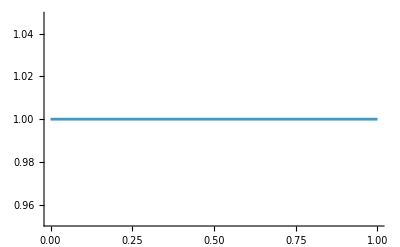

```mathematica
Clear["Global`*"]
P=Solve[{b1==r1*a1+I*t1*x1,y1==I*t1*a1+r1*x1,b2==r2*a2+I*t2*x2,y2==I*t2*a2+r2*x2,b3==r3*a3+I*t3*x3,y3==I*t3*a3+r3*x3,b4==r4*a4+I*t4*x4,y4==I*t4*a4+r4*x4,x1==y4,x3==q*y1+p*y2,x2==p*y1+q*y2,y3==x4},{b1,b2,b3,b4,y1,y2,y3,y4,x1,x2,x3,x4}];
b1=b1/.P[[1]];
b2=b2/.P[[1]];
b3=b3/.P[[1]];
b4=b4/.P[[1]];
s11=b1/.{a1->1,a2->0,a3->0,a4->0}//FullSimplify;
s12=b1/.{a1->0,a2->1,a3->0,a4->0}//FullSimplify;
s13=b1/.{a1->0,a2->0,a3->1,a4->0}//FullSimplify;
s14=b1/.{a1->0,a2->0,a3->0,a4->1}//FullSimplify;
s21=b2/.{a1->1,a2->0,a3->0,a4->0}//FullSimplify;
s22=b2/.{a1->0,a2->1,a3->0,a4->0}//FullSimplify;
s23=b2/.{a1->0,a2->0,a3->1,a4->0}//FullSimplify;
s24=b2/.{a1->0,a2->0,a3->0,a4->1}//FullSimplify;
s31=b3/.{a1->1,a2->0,a3->0,a4->0}//FullSimplify;
s32=b3/.{a1->0,a2->1,a3->0,a4->0}//FullSimplify;
s33=b3/.{a1->0,a2->0,a3->1,a4->0}//FullSimplify;
s34=b3/.{a1->0,a2->0,a3->0,a4->1}//FullSimplify;
s41=b4/.{a1->1,a2->0,a3->0,a4->0}//FullSimplify;
s42=b4/.{a1->0,a2->1,a3->0,a4->0}//FullSimplify;
s43=b4/.{a1->0,a2->0,a3->1,a4->0}//FullSimplify;
s44=b4/.{a1->0,a2->0,a3->0,a4->1}//FullSimplify;
s={{s11,s12,s13,s14},{s21,s22,s23,s24},{s31,s32,s33,s34},{s41,s42,s43,s44}};
r1=√R1;
t1=√(1-R1);
r2=√R2;
t2=√(1-R2);
r3=√R3;
t3=√(1-R3);
r4=√R4;
t4=√(1-R4);
T11=Abs[s11]^2;
T12=Abs[s12]^2;
T13=Abs[s13]^2;
T14=Abs[s14]^2;
T21=Abs[s21]^2;
T22=Abs[s22]^2;
T23=Abs[s23]^2;
T24=Abs[s24]^2;
T31=Abs[s31]^2;
T32=Abs[s32]^2;
T33=Abs[s33]^2;
T34=Abs[s34]^2;
T41=Abs[s41]^2;
T42=Abs[s42]^2;
T43=Abs[s43]^2;
T44=Abs[s44]^2;
R1=0.9;
R2=0.4;
R3=0.2;
R4=0.8;
p=I √ϵ;
q=√(1-ϵ);
Plot[T11+T12+T13+T14,{ϵ,0,1}]
```

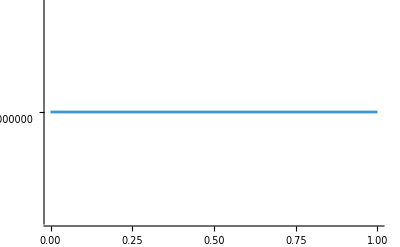

```mathematica
Plot[T21+T22+T23+T24,{ϵ,0,1}]
```

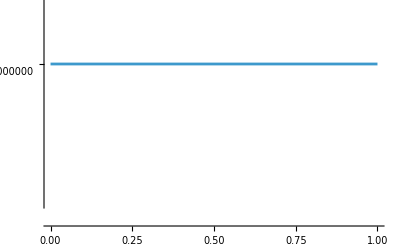

```mathematica
Plot[T31+T32+T33+T34,{ϵ,0,1}]
```

```mathematica
Plot[T41+T42+T43+T44,{ϵ,0,1}]
```

-Graphics-

```mathematica
s={{s11,s12,s13,s14},{s21,s22,s23,s24},{s31,s32,s33,s34},{s41,s42,s43,s44}};
Chop[s.Transpose[Conjugate[s]]/.{ϵ->0.5}]
```

{{1.,0,0,0},{0,1.,0,0},{0,0,1.,0},{0,0,0,1.}}

# Four-terminal disordered QSH setup with Buttiker Voltage-probe with momentum and phase relaxation probability conservation and unitarity of s-matrix

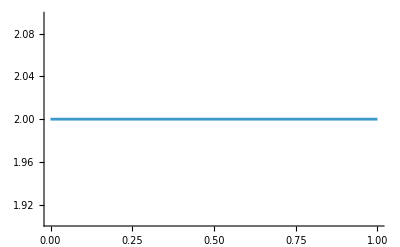

```mathematica
Clear["Global`*"]
P=Solve[{b1u==r1*a1u+I*t1*x1u,y1u==I*t1*a1u+r1*x1u,b2u==r2*a2u+I*t2*x2u,y2u==I*t2*a2u+r2*x2u,b3u==r3*a3u+I*t3*x3u,y3u==I*t3*a3u+r3*x3u,b4u==r4*a4u+I*t4*x4u,y4u==I*t4*a4u+r4*x4u,x1u==y4u,x3u==q*y1u+p*y2u,x2u==p*y1u+q*y2u,y3u==x4u,(*d sector*)b1d==r1*a1d+I*t1*x1d,y1d==I*t1*a1d+r1*x1d,b2d==r2*a2d+I*t2*x2d,y2d==I*t2*a2d+r2*x2d,b3d==r3*a3d+I*t3*x3d,y3d==I*t3*a3d+r3*x3d,b4d==r4*a4d+I*t4*x4d,y4d==I*t4*a4d+r4*x4d,x1d==q*y3d+p*y2d,x4d==y1d,x2d==p*y3d+q*y2d,y4d==x3d},{b1u,b2u,b3u,b4u,y1u,y2u,y3u,y4u,x1u,x2u,x3u,x4u,b1d,b2d,b3d,b4d,y1d,y2d,y3d,y4d,x1d,x2d,x3d,x4d}];
b1u=b1u/.P[[1]];
b2u=b2u/.P[[1]];
b3u=b3u/.P[[1]];
b4u=b4u/.P[[1]];
b1d=b1d/.P[[1]];
b2d=b2d/.P[[1]];
b3d=b3d/.P[[1]];
b4d=b4d/.P[[1]];
s11uu=b1u/.{a1u->1,a2u->0,a3u->0,a4u->0}//FullSimplify;
s12uu=b1u/.{a1u->0,a2u->1,a3u->0,a4u->0}//FullSimplify;
s13uu=b1u/.{a1u->0,a2u->0,a3u->1,a4u->0}//FullSimplify;
s14uu=b1u/.{a1u->0,a2u->0,a3u->0,a4u->1}//FullSimplify;
s21uu=b2u/.{a1u->1,a2u->0,a3u->0,a4u->0}//FullSimplify;
s22uu=b2u/.{a1u->0,a2u->1,a3u->0,a4u->0}//FullSimplify;
s23uu=b2u/.{a1u->0,a2u->0,a3u->1,a4u->0}//FullSimplify;
s24uu=b2u/.{a1u->0,a2u->0,a3u->0,a4u->1}//FullSimplify;
s31uu=b3u/.{a1u->1,a2u->0,a3u->0,a4u->0}//FullSimplify;
s32uu=b3u/.{a1u->0,a2u->1,a3u->0,a4u->0}//FullSimplify;
s33uu=b3u/.{a1u->0,a2u->0,a3u->1,a4u->0}//FullSimplify;
s34uu=b3u/.{a1u->0,a2u->0,a3u->0,a4u->1}//FullSimplify;
s41uu=b4u/.{a1u->1,a2u->0,a3u->0,a4u->0}//FullSimplify;
s42uu=b4u/.{a1u->0,a2u->1,a3u->0,a4u->0}//FullSimplify;
s43uu=b4u/.{a1u->0,a2u->0,a3u->1,a4u->0}//FullSimplify;
s44uu=b4u/.{a1u->0,a2u->0,a3u->0,a4u->1}//FullSimplify;
s11dd=b1d/. {a1d->1,a2d->0,a3d->0,a4d->0}//FullSimplify;
s12dd=b1d/. {a1d->0,a2d->1,a3d->0,a4d->0}//FullSimplify;
s13dd=b1d/. {a1d->0,a2d->0,a3d->1,a4d->0}//FullSimplify;
s14dd=b1d/. {a1d->0,a2d->0,a3d->0,a4d->1}//FullSimplify;
s21dd=b2d/. {a1d->1,a2d->0,a3d->0,a4d->0}//FullSimplify;
s22dd=b2d/. {a1d->0,a2d->1,a3d->0,a4d->0}//FullSimplify;
s23dd=b2d/. {a1d->0,a2d->0,a3d->1,a4d->0}//FullSimplify;
s24dd=b2d/. {a1d->0,a2d->0,a3d->0,a4d->1}//FullSimplify;s31dd=b3d/. {a1d->1,a2d->0,a3d->0,a4d->0}//FullSimplify;
s32dd=b3d/. {a1d->0,a2d->1,a3d->0,a4d->0}//FullSimplify;
s33dd=b3d/. {a1d->0,a2d->0,a3d->1,a4d->0}//FullSimplify;
s34dd=b3d/. {a1d->0,a2d->0,a3d->0,a4d->1}//FullSimplify;
s41dd=b4d/. {a1d->1,a2d->0,a3d->0,a4d->0}//FullSimplify;
s42dd=b4d/. {a1d->0,a2d->1,a3d->0,a4d->0}//FullSimplify;
s43dd=b4d/. {a1d->0,a2d->0,a3d->1,a4d->0}//FullSimplify;
s44dd=b4d/. {a1d->0,a2d->0,a3d->0,a4d->1}//FullSimplify;
s={{s11,s12,s13,s14},{s21,s22,s23,s24},{s31,s32,s33,s34},{s41,s42,s43,s44}};
r1=√R1;
t1=√(1-R1);
r2=√R2;
t2=√(1-R2);
r3=√R3;
t3=√(1-R3);
r4=√R4;
t4=√(1-R4);
T11uu=Abs[s11uu]^2;
T12uu=Abs[s12uu]^2;
T13uu=Abs[s13uu]^2;
T14uu=Abs[s14uu]^2;
T21uu=Abs[s21uu]^2;
T22uu=Abs[s22uu]^2;
T23uu=Abs[s23uu]^2;
T24uu=Abs[s24uu]^2;
T31uu=Abs[s31uu]^2;
T32uu=Abs[s32uu]^2;
T33uu=Abs[s33uu]^2;
T34uu=Abs[s34uu]^2;
T41uu=Abs[s41uu]^2;
T42uu=Abs[s42uu]^2;
T43uu=Abs[s43uu]^2;
T44uu=Abs[s44uu]^2;
T11dd=Abs[s11dd]^2;
T12dd=Abs[s12dd]^2;
T13dd=Abs[s13dd]^2;
T14dd=Abs[s14dd]^2;
T21dd=Abs[s21dd]^2;
T22dd=Abs[s22dd]^2;
T23dd=Abs[s23dd]^2;
T24dd=Abs[s24dd]^2;
T31dd=Abs[s31dd]^2;
T32dd=Abs[s32dd]^2;
T33dd=Abs[s33dd]^2;
T34dd=Abs[s34dd]^2;
T41dd=Abs[s41dd]^2;
T42dd=Abs[s42dd]^2;
T43dd=Abs[s43dd]^2;
T44dd=Abs[s44dd]^2;
T11=T11uu+T11dd;
T12=T12uu+T12dd;
T13=T13uu+T13dd;
T14=T14uu+T14dd;
T21=T21uu+T21dd;
T22=T22uu+T22dd;
T23=T23uu+T23dd;
T24=T24uu+T24dd;
T31=T31uu+T31dd;
T32=T32uu+T32dd;
T33=T33uu+T33dd;
T34=T34uu+T34dd;
T41=T41uu+T41dd;
T42=T42uu+T42dd;
T43=T43uu+T43dd;
T44=T44uu+T44dd;
R1=0.9;
R2=0.4;
R3=0.2;
R4=0.8;
p=I √ϵ;
q=√(1-ϵ);
Plot[T11+T12+T13+T14,{ϵ,0,1}]
```

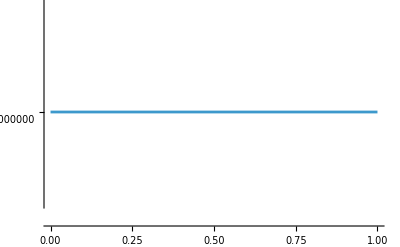

```mathematica
Plot[T21+T22+T23+T24,{ϵ,0,1}]
```

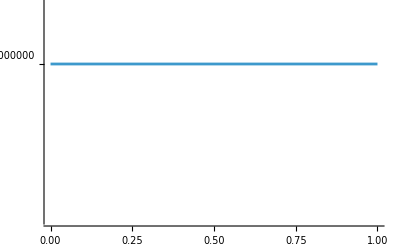

```mathematica
Plot[T31+T32+T33+T34,{ϵ,0,1}]
```

```mathematica
Plot[T41+T42+T43+T44,{ϵ,0,1}]
```

-Graphics-

```mathematica
s={{s11uu,0,s12uu,0,s13uu,0,s14uu,0},{0,s11dd,0,s12dd,0,s13dd,0,s14dd},{s21uu,0,s22uu,0,s23uu,0,s24uu,0},{0,s21dd,0,s22dd,0,s23dd,0,s24dd},{s31uu,0,s32uu,0,s33uu,0,s34uu,0},{0,s31dd,0,s32dd,0,s33dd,0,s34dd}{s41uu,0,s42uu,0,s43uu,0,s44uu,0},{0,s41dd,0,s42dd,0,s43dd,0,s44dd}};
Chop[s.Transpose[Conjugate[s]]/.{ϵ->0.5}]
```

{{1.,0,0,0,0,0,0},{0,1.,0,0,0,0,0},{0,0,1.,0,0,0,0},{0,0,0,1.,0,0,0},{0,0,0,0,1.,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,1.}}

# Four-terminal disordered QH setup with Buttiker Voltage-probe with momentum and phase relaxation (Analytical expression of Quantum shot noise)

```mathematica
Clear["Global`*"]
P=Solve[{b1==r1*a1+I*t1*x1,y1==I*t1*a1+r1*x1,b2==r2*a2+I*t2*x2,y2==I*t2*a2+r2*x2,b3==r3*a3+I*t3*x3,y3==I*t3*a3+r3*x3,b4==r4*a4+I*t4*x4,y4==I*t4*a4+r4*x4,x1==y4,x3==q*y1+p*y2,x2==p*y1+q*y2,y3==x4},{b1,b2,b3,b4,y1,y2,y3,y4,x1,x2,x3,x4}];
b1=b1/.P[[1]];
b2=b2/.P[[1]];
b3=b3/.P[[1]];
b4=b4/.P[[1]];
s11=b1/.{a1->1,a2->0,a3->0,a4->0}//FullSimplify;
s12=b1/.{a1->0,a2->1,a3->0,a4->0}//FullSimplify;
s13=b1/.{a1->0,a2->0,a3->1,a4->0}//FullSimplify;
s14=b1/.{a1->0,a2->0,a3->0,a4->1}//FullSimplify;
s21=b2/.{a1->1,a2->0,a3->0,a4->0}//FullSimplify;
s22=b2/.{a1->0,a2->1,a3->0,a4->0}//FullSimplify;
s23=b2/.{a1->0,a2->0,a3->1,a4->0}//FullSimplify;
s24=b2/.{a1->0,a2->0,a3->0,a4->1}//FullSimplify;
s31=b3/.{a1->1,a2->0,a3->0,a4->0}//FullSimplify;
s32=b3/.{a1->0,a2->1,a3->0,a4->0}//FullSimplify;
s33=b3/.{a1->0,a2->0,a3->1,a4->0}//FullSimplify;
s34=b3/.{a1->0,a2->0,a3->0,a4->1}//FullSimplify;
s41=b4/.{a1->1,a2->0,a3->0,a4->0}//FullSimplify;
s42=b4/.{a1->0,a2->1,a3->0,a4->0}//FullSimplify;
s43=b4/.{a1->0,a2->0,a3->1,a4->0}//FullSimplify;
s44=b4/.{a1->0,a2->0,a3->0,a4->1}//FullSimplify;
s={{s11,s12,s13,s14},{s21,s22,s23,s24},{s31,s32,s33,s34},{s41,s42,s43,s44}};
r1=√R1;
t1=√(1-R1);
r2=√R2;
t2=√(1-R2);
r3=√R3;
t3=√(1-R3);
r4=√R4;
t4=√(1-R4);
T11=Abs[s11]^2;
T12=Abs[s12]^2;
T13=Abs[s13]^2;
T14=Abs[s14]^2;
T21=Abs[s21]^2;
T22=Abs[s22]^2;
T23=Abs[s23]^2;
T24=Abs[s24]^2;
T31=Abs[s31]^2;
T32=Abs[s32]^2;
T33=Abs[s33]^2;
T34=Abs[s34]^2;
T41=Abs[s41]^2;
T42=Abs[s42]^2;
T43=Abs[s43]^2;
T44=Abs[s44]^2;
R1=0.9;
R2=0.4;
R3=0.2;
R4=0.8;
T=0.001;
df=Exp[(G)/(kb1)]/((Exp[(G)/(kb1)]+1)^2  kb1);
kb1=T;
p=I √ϵ;
q=√(1-ϵ);
f1=1/(1+Exp[(G-V)/T]);
f2=1/(1+Exp[(G-V2)/T]);
f3=f4=1/(1+Exp[(G-V3)/T]);
V=2;
V3=0;
G31=-T31;
G32=-T32;
G33=(1-T33);
G34=-T34;
G13=-T13;
G14=-T14;
G21=-T21;
G23=-T23;
G24=-T24;
G11=(1-T11);
G21=-T21;
G12=(-T12);
G22=(1-T22);
G41=-T41;
G42=-T42;
G43=(-T43);
G44=(1-T44);
V2=-G21/G22*V;
SetSharedVariable[list1]
list1={};
ParallelDo[{
S340=(1+G21/G22)(2*Re[s31 s42 Conjugate[s32] Conjugate[s41]])+(2Re[s31 s43 Conjugate[s33] Conjugate[s41]])+(2Re[s31 s44 Conjugate[s34] Conjugate[s41]])-G21/G22(2Re[s32 s43 Conjugate[s33] Conjugate[s42]]+2Re[s32 s44 Conjugate[s34] Conjugate[s42]]);
S240=(1+G21/G22)(2*Re[s21 s42 Conjugate[s22] Conjugate[s41]])+(2Re[s21 s43 Conjugate[s23] Conjugate[s41]])+(2Re[s21 s44 Conjugate[s24] Conjugate[s41]])-G21/G22(2Re[s22 s43 Conjugate[s23] Conjugate[s42]]+2Re[s22 s44 Conjugate[s24] Conjugate[s42]]);
S230=(1+G21/G22)(2*Re[s21 s32 Conjugate[s22] Conjugate[s31]])+(2Re[s21 s33 Conjugate[s23] Conjugate[s31]])+(2Re[s21 s34 Conjugate[s24] Conjugate[s31]])-G21/G22(2Re[s22 s33 Conjugate[s23] Conjugate[s32]]+2Re[s22 s34 Conjugate[s24] Conjugate[s32]]);
S220=(1+G21/G22)(2*Re[s21 s22 Conjugate[s22] Conjugate[s21]])+(2Re[s21 s23 Conjugate[s23] Conjugate[s21]])+(2Re[s21 s24 Conjugate[s24] Conjugate[s21]])-G21/G22(2Re[s22 s23 Conjugate[s23] Conjugate[s22]]+2Re[s22 s24 Conjugate[s24] Conjugate[s22]]);
S34in=(S340-(G32/G22) S240-(G42/G22) S230+(G32*G42/G22^2) S220)/2;
A1=(S340-(G32/G22) S240-(G42/G22) S230)/2;
A2=(G32*G42/G22^2) S220/2;
G3eff=G31-(G32*G21)/G22;
G4eff=G41-(G42*G21)/G22;
F34in=S34in/(2Sqrt[G3eff*G4eff]);
list=AppendTo[list1,{ϵ,Re[S11in]/(2V),Re[S13in]/(2V),Re[S14in]/(2V),Re[S33in]/(2V),Re[S34in],F34in,Re[A1],Re[A2],Re[S44in]/(2V),Re[S11in+S13in+S14in],Re[S13in+S33in+S34in],Re[S14in+S34in+S44in]}];
},{ϵ,0.01,1,0.01}];//AbsoluteTiming
listn=Sort[list1];
Export["Shot1ad4check.dat",listn]
```

{0.347936,Null}

Shot1ad4check.dat

# Four-terminal disordered QSH setup with Buttiker Voltage-probe with momentum and phase relaxation (Analytical expression of Quantum shot noise Analytical)

```mathematica
Clear["Global`*"]
P=Solve[{b1u==r1*a1u+I*t1*x1u,y1u==I*t1*a1u+r1*x1u,b2u==r2*a2u+I*t2*x2u,y2u==I*t2*a2u+r2*x2u,b3u==r3*a3u+I*t3*x3u,y3u==I*t3*a3u+r3*x3u,b4u==r4*a4u+I*t4*x4u,y4u==I*t4*a4u+r4*x4u,x1u==y4u,x3u==q*y1u+p*y2u,x2u==p*y1u+q*y2u,y3u==x4u,(*d sector*)b1d==r1*a1d+I*t1*x1d,y1d==I*t1*a1d+r1*x1d,b2d==r2*a2d+I*t2*x2d,y2d==I*t2*a2d+r2*x2d,b3d==r3*a3d+I*t3*x3d,y3d==I*t3*a3d+r3*x3d,b4d==r4*a4d+I*t4*x4d,y4d==I*t4*a4d+r4*x4d,x1d==q*y3d+p*y2d,x4d==y1d,x2d==p*y3d+q*y2d,y4d==x3d},{b1u,b2u,b3u,b4u,y1u,y2u,y3u,y4u,x1u,x2u,x3u,x4u,b1d,b2d,b3d,b4d,y1d,y2d,y3d,y4d,x1d,x2d,x3d,x4d}];
b1u=b1u/.P[[1]];
b2u=b2u/.P[[1]];
b3u=b3u/.P[[1]];
b4u=b4u/.P[[1]];
b1d=b1d/.P[[1]];
b2d=b2d/.P[[1]];
b3d=b3d/.P[[1]];
b4d=b4d/.P[[1]];
s11uu=b1u/.{a1u->1,a2u->0,a3u->0,a4u->0}//FullSimplify;
s12uu=b1u/.{a1u->0,a2u->1,a3u->0,a4u->0}//FullSimplify;
s13uu=b1u/.{a1u->0,a2u->0,a3u->1,a4u->0}//FullSimplify;
s14uu=b1u/.{a1u->0,a2u->0,a3u->0,a4u->1}//FullSimplify;
s21uu=b2u/.{a1u->1,a2u->0,a3u->0,a4u->0}//FullSimplify;
s22uu=b2u/.{a1u->0,a2u->1,a3u->0,a4u->0}//FullSimplify;
s23uu=b2u/.{a1u->0,a2u->0,a3u->1,a4u->0}//FullSimplify;
s24uu=b2u/.{a1u->0,a2u->0,a3u->0,a4u->1}//FullSimplify;
s31uu=b3u/.{a1u->1,a2u->0,a3u->0,a4u->0}//FullSimplify;
s32uu=b3u/.{a1u->0,a2u->1,a3u->0,a4u->0}//FullSimplify;
s33uu=b3u/.{a1u->0,a2u->0,a3u->1,a4u->0}//FullSimplify;
s34uu=b3u/.{a1u->0,a2u->0,a3u->0,a4u->1}//FullSimplify;
s41uu=b4u/.{a1u->1,a2u->0,a3u->0,a4u->0}//FullSimplify;
s42uu=b4u/.{a1u->0,a2u->1,a3u->0,a4u->0}//FullSimplify;
s43uu=b4u/.{a1u->0,a2u->0,a3u->1,a4u->0}//FullSimplify;
s44uu=b4u/.{a1u->0,a2u->0,a3u->0,a4u->1}//FullSimplify;
s11dd=b1d/. {a1d->1,a2d->0,a3d->0,a4d->0}//FullSimplify;
s12dd=b1d/. {a1d->0,a2d->1,a3d->0,a4d->0}//FullSimplify;
s13dd=b1d/. {a1d->0,a2d->0,a3d->1,a4d->0}//FullSimplify;
s14dd=b1d/. {a1d->0,a2d->0,a3d->0,a4d->1}//FullSimplify;
s21dd=b2d/. {a1d->1,a2d->0,a3d->0,a4d->0}//FullSimplify;
s22dd=b2d/. {a1d->0,a2d->1,a3d->0,a4d->0}//FullSimplify;
s23dd=b2d/. {a1d->0,a2d->0,a3d->1,a4d->0}//FullSimplify;
s24dd=b2d/. {a1d->0,a2d->0,a3d->0,a4d->1}//FullSimplify;s31dd=b3d/. {a1d->1,a2d->0,a3d->0,a4d->0}//FullSimplify;
s32dd=b3d/. {a1d->0,a2d->1,a3d->0,a4d->0}//FullSimplify;
s33dd=b3d/. {a1d->0,a2d->0,a3d->1,a4d->0}//FullSimplify;
s34dd=b3d/. {a1d->0,a2d->0,a3d->0,a4d->1}//FullSimplify;
s41dd=b4d/. {a1d->1,a2d->0,a3d->0,a4d->0}//FullSimplify;
s42dd=b4d/. {a1d->0,a2d->1,a3d->0,a4d->0}//FullSimplify;
s43dd=b4d/. {a1d->0,a2d->0,a3d->1,a4d->0}//FullSimplify;
s44dd=b4d/. {a1d->0,a2d->0,a3d->0,a4d->1}//FullSimplify;
s={{s11,s12,s13,s14},{s21,s22,s23,s24},{s31,s32,s33,s34},{s41,s42,s43,s44}};
r1=√R1;
t1=√(1-R1);
r2=√R2;
t2=√(1-R2);
r3=√R3;
t3=√(1-R3);
r4=√R4;
t4=√(1-R4);
T11uu=Abs[s11uu]^2;
T12uu=Abs[s12uu]^2;
T13uu=Abs[s13uu]^2;
T14uu=Abs[s14uu]^2;
T21uu=Abs[s21uu]^2;
T22uu=Abs[s22uu]^2;
T23uu=Abs[s23uu]^2;
T24uu=Abs[s24uu]^2;
T31uu=Abs[s31uu]^2;
T32uu=Abs[s32uu]^2;
T33uu=Abs[s33uu]^2;
T34uu=Abs[s34uu]^2;
T41uu=Abs[s41uu]^2;
T42uu=Abs[s42uu]^2;
T43uu=Abs[s43uu]^2;
T44uu=Abs[s44uu]^2;
T11dd=Abs[s11dd]^2;
T12dd=Abs[s12dd]^2;
T13dd=Abs[s13dd]^2;
T14dd=Abs[s14dd]^2;
T21dd=Abs[s21dd]^2;
T22dd=Abs[s22dd]^2;
T23dd=Abs[s23dd]^2;
T24dd=Abs[s24dd]^2;
T31dd=Abs[s31dd]^2;
T32dd=Abs[s32dd]^2;
T33dd=Abs[s33dd]^2;
T34dd=Abs[s34dd]^2;
T41dd=Abs[s41dd]^2;
T42dd=Abs[s42dd]^2;
T43dd=Abs[s43dd]^2;
T44dd=Abs[s44dd]^2;
T11=T11uu+T11dd;
T12=T12uu+T12dd;
T13=T13uu+T13dd;
T14=T14uu+T14dd;
T21=T21uu+T21dd;
T21s=T21uu-T21dd;
T22=T22uu+T22dd;
T22s=T22uu-T22dd;
T23=T23uu+T23dd;
T24=T24uu+T24dd;
T31=T31uu+T31dd;
T31s=T31uu-T31dd;
T32=T32uu+T32dd;
T32s=T32uu-T32dd;
T33=T33uu+T33dd;
T34=T34uu+T34dd;
T41=T41uu+T41dd;
T41s=T41uu-T41dd;
T42=T42uu+T42dd;
T42s=T42uu-T42dd;
T43=T43uu+T43dd;
T44=T44uu+T44dd;
R1=0.9;
R2=0.4;
R3=0.2;
R4=0.8;
T=0.001;
df=Exp[(G)/(kb1)]/((Exp[(G)/(kb1)]+1)^2  kb1);
kb1=T;
p=I √ϵ;
q=√(1-ϵ);
f1=1/(1+Exp[(G-V)/T]);
f2=1/(1+Exp[(G-V2)/T]);
f3=f4=1/(1+Exp[(G-V3)/T]);
V=2;
V3=0;
G31=-T31;
G31s=-T31s;
G32s=-T32s;
G21s=-T21s;
G41s=-T41s;
G42s=-T42s;

G32=-T32;
G33=(2-T33);
G34=-T34;
G13=-T13;
G14=-T14;
G23=-T23;
G24=-T24;
G11=(2-T11);
G21=-T21;
G12=(-T12);
G22=(2-T22);
G22s=-T22s;
G41=-T41;
G42=-T42;
G43=(-T43);
G44=(2-T44);
V2=-G21/G22*V;
SetSharedVariable[list1]
list1={};
ParallelDo[{
S340=(1+G21/G22) ((2 Re[s31uu s42uu Conjugate[s32uu] Conjugate[s41uu]])+(2 Re[s31dd s42dd Conjugate[s32dd] Conjugate[s41dd]]))+((2 Re[s31uu s43uu Conjugate[s33uu] Conjugate[s41uu]])+(2 Re[s31dd s43dd Conjugate[s33dd] Conjugate[s41dd]]))+((2 Re[s31uu s44uu Conjugate[s34uu] Conjugate[s41uu]])+(2 Re[s31dd s44dd Conjugate[s34dd] Conjugate[s41dd]]))-G21/G22 (((2 Re[s32uu s43uu Conjugate[s33uu] Conjugate[s42uu]])+(2 Re[s32dd s43dd Conjugate[s33dd] Conjugate[s42dd]]))+((2 Re[s32uu s44uu Conjugate[s34uu] Conjugate[s42uu]])+(2 Re[s32dd s44dd Conjugate[s34dd] Conjugate[s42dd]])));

S240=(1+G21/G22) ((2 Re[s21uu s42uu Conjugate[s22uu] Conjugate[s41uu]])+(2 Re[s21dd s42dd Conjugate[s22dd] Conjugate[s41dd]]))+((2 Re[s21uu s43uu Conjugate[s23uu] Conjugate[s41uu]])+(2 Re[s21dd s43dd Conjugate[s23dd] Conjugate[s41dd]]))+((2 Re[s21uu s44uu Conjugate[s24uu] Conjugate[s41uu]])+(2 Re[s21dd s44dd Conjugate[s24dd] Conjugate[s41dd]]))-G21/G22 (((2 Re[s22uu s43uu Conjugate[s23uu] Conjugate[s42uu]])+(2 Re[s22dd s43dd Conjugate[s23dd] Conjugate[s42dd]]))+((2 Re[s22uu s44uu Conjugate[s24uu] Conjugate[s42uu]])+(2 Re[s22dd s44dd Conjugate[s24dd] Conjugate[s42dd]])));

S230=(1+G21/G22) ((2 Re[s21uu s32uu Conjugate[s22uu] Conjugate[s31uu]])+(2 Re[s21dd s32dd Conjugate[s22dd] Conjugate[s31dd]]))+((2 Re[s21uu s33uu Conjugate[s23uu] Conjugate[s31uu]])+(2 Re[s21dd s33dd Conjugate[s23dd] Conjugate[s31dd]]))+((2 Re[s21uu s34uu Conjugate[s24uu] Conjugate[s31uu]])+(2 Re[s21dd s34dd Conjugate[s24dd] Conjugate[s31dd]]))-G21/G22 (((2 Re[s22uu s33uu Conjugate[s23uu] Conjugate[s32uu]])+(2 Re[s22dd s33dd Conjugate[s23dd] Conjugate[s32dd]]))+((2 Re[s22uu s34uu Conjugate[s24uu] Conjugate[s32uu]])+(2 Re[s22dd s34dd Conjugate[s24dd] Conjugate[s32dd]])));

S220=(1+G21/G22) ((2 Re[s21uu s22uu Conjugate[s22uu] Conjugate[s21uu]])+(2 Re[s21dd s22dd Conjugate[s22dd] Conjugate[s21dd]]))+((2 Re[s21uu s23uu Conjugate[s23uu] Conjugate[s21uu]])+(2 Re[s21dd s23dd Conjugate[s23dd] Conjugate[s21dd]]))+((2 Re[s21uu s24uu Conjugate[s24uu] Conjugate[s21uu]])+(2 Re[s21dd s24dd Conjugate[s24dd] Conjugate[s21dd]]))-G21/G22 (((2 Re[s22uu s23uu Conjugate[s23uu] Conjugate[s22uu]])+(2 Re[s22dd s23dd Conjugate[s23dd] Conjugate[s22dd]]))+((2 Re[s22uu s24uu Conjugate[s24uu] Conjugate[s22uu]])+(2 Re[s22dd s24dd Conjugate[s24dd] Conjugate[s22dd]])));
S34in=(S340-(G32/G22) S240-(G42/G22) S230+(G32*G42/G22^2) S220)/2;
A1=(S340-(G32/G22) S240-(G42/G22) S230)/2;
A2=(G32*G42/G22^2) S220/2;
G3eff=G31-(G32*G21)/G22;
G4eff=G41-(G42*G21)/G22;
G3effs=G31s-(G32s*G21s)/G22s;
G4effs=G41s-(G42s*G21s)/G22s;
F34in=S34in/(2Sqrt[G3eff*G4eff]);
F34ins=S34in/(2Sqrt[Abs[G3effs]*Abs[G4effs]]);
list=AppendTo[list1,{ϵ,Re[S11in]/(2V),Re[S13in]/(2V),Re[S14in]/(2V),Re[S33in]/(2V),Re[S34in],F34in,Re[A1],Re[A2],Re[F34ins],Re[S44in]/(2V),Re[S11in+S13in+S14in],Re[S13in+S33in+S34in],Re[S14in+S34in+S44in]}];
},{ϵ,0.01,1,0.01}];//AbsoluteTiming
listn=Sort[list1];
Export["Shot1ad4scheck.dat",listn]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{1.03277,Null}

Shot1ad4scheck.dat

# Four-terminal disordered QH setup with Buttiker Voltage-temperature probe with momentum and phase relaxation (Δ_T noise Analytical)

```mathematica
Clear["Global`*"]
P=Solve[{b1==r1*a1+I*t1*x1,y1==I*t1*a1+r1*x1,b2==r2*a2+I*t2*x2,y2==I*t2*a2+r2*x2,b3==r3*a3+I*t3*x3,y3==I*t3*a3+r3*x3,b4==r4*a4+I*t4*x4,y4==I*t4*a4+r4*x4,x1==y4,x3==q*y1+p*y2,x2==p*y1+q*y2,y3==x4},{b1,b2,b3,b4,y1,y2,y3,y4,x1,x2,x3,x4}];
b1=b1/.P[[1]];
b2=b2/.P[[1]];
b3=b3/.P[[1]];
b4=b4/.P[[1]];
s11=b1/.{a1->1,a2->0,a3->0,a4->0}//FullSimplify;
s12=b1/.{a1->0,a2->1,a3->0,a4->0}//FullSimplify;
s13=b1/.{a1->0,a2->0,a3->1,a4->0}//FullSimplify;
s14=b1/.{a1->0,a2->0,a3->0,a4->1}//FullSimplify;
s21=b2/.{a1->1,a2->0,a3->0,a4->0}//FullSimplify;
s22=b2/.{a1->0,a2->1,a3->0,a4->0}//FullSimplify;
s23=b2/.{a1->0,a2->0,a3->1,a4->0}//FullSimplify;
s24=b2/.{a1->0,a2->0,a3->0,a4->1}//FullSimplify;
s31=b3/.{a1->1,a2->0,a3->0,a4->0}//FullSimplify;
s32=b3/.{a1->0,a2->1,a3->0,a4->0}//FullSimplify;
s33=b3/.{a1->0,a2->0,a3->1,a4->0}//FullSimplify;
s34=b3/.{a1->0,a2->0,a3->0,a4->1}//FullSimplify;
s41=b4/.{a1->1,a2->0,a3->0,a4->0}//FullSimplify;
s42=b4/.{a1->0,a2->1,a3->0,a4->0}//FullSimplify;
s43=b4/.{a1->0,a2->0,a3->1,a4->0}//FullSimplify;
s44=b4/.{a1->0,a2->0,a3->0,a4->1}//FullSimplify;
s={{s11,s12,s13,s14},{s21,s22,s23,s24},{s31,s32,s33,s34},{s41,s42,s43,s44}};
r1=√R1;
t1=√(1-R1);
r2=√R2;
t2=√(1-R2);
r3=√R3;
t3=√(1-R3);
r4=√R4;
t4=√(1-R4);
T11=Abs[s11]^2;
T12=Abs[s12]^2;
T13=Abs[s13]^2;
T14=Abs[s14]^2;
T21=Abs[s21]^2;
T22=Abs[s22]^2;
T23=Abs[s23]^2;
T24=Abs[s24]^2;
T31=Abs[s31]^2;
T32=Abs[s32]^2;
T33=Abs[s33]^2;
T34=Abs[s34]^2;
T41=Abs[s41]^2;
T42=Abs[s42]^2;
T43=Abs[s43]^2;
T44=Abs[s44]^2;
R1=0.9;
R2=0.4;
R3=0.2;
R4=0.8;
T=10;
df=Exp[(G)/(kb1)]/((Exp[(G)/(kb1)]+1)^2  kb1);
kb1=T;
p=I √ϵ;
q=√(1-ϵ);
f1=1/(1+Exp[(G-V)/T1]);
f2=1/(1+Exp[(G-V2)/T2]);
f3=f4=1/(1+Exp[(G-V3)/T3]);
V2=V3=V4=V1=0;
V=0;
T1=T+0.1*T/2;
T3=T-0.1*T/2;
T2=T+dt;
SetSharedVariable[list1]
list1={};
ParallelDo[{
K31=NIntegrate[-T31*G^2 df,{G,-20T,20T}];
K32=NIntegrate[-T32*G^2 df,{G,-20T,20T}];
K33=NIntegrate[(1-T33)*G^2 df,{G,-20T,20T}];
K34=NIntegrate[-T34*G^2 df,{G,-20T,20T}];
K13=NIntegrate[-T13*G^2 df,{G,-20T,20T}];
K14=NIntegrate[-T14*G^2 df,{G,-20T,20T}];
K21=NIntegrate[-T21*G^2 df,{G,-20T,20T}];
K23=NIntegrate[-T23*G^2 df,{G,-20T,20T}];
K24=NIntegrate[-T24*G^2 df,{G,-20T,20T}];
K11=NIntegrate[(1-T11)*G^2 df,{G,-20T,20T}];
K21=NIntegrate[-T21*G^2 df,{G,-20T,20T}];
K12=NIntegrate[(-T12)*G^2 df,{G,-20T,20T}];
K22=NIntegrate[(1-T22)*G^2 df,{G,-20T,20T}];
K41=NIntegrate[-T41*G^2 df,{G,-20T,20T}];
K42=NIntegrate[-T42*G^2 df,{G,-20T,20T}];
K43=NIntegrate[(-T43)*G^2 df,{G,-20T,20T}];
K44=NIntegrate[(1-T44)*G^2 df,{G,-20T,20T}];
dt=(-K21*0.1*T/2+K23*0.1*T/2+K24*0.1*T/2)/K22;
G31=NIntegrate[-T31*df,{G,-20T,20T}];
G32=NIntegrate[-T32*df,{G,-20T,20T}];
G33=NIntegrate[(1-T33)*df,{G,-20T,20T}];
G34=NIntegrate[-T34*df,{G,-20T,20T}];
G13=NIntegrate[-T13*df,{G,-20T,20T}];
G14=NIntegrate[-T14*df,{G,-20T,20T}];
G23=NIntegrate[-T23*df,{G,-20T,20T}];
G24=NIntegrate[-T24*df,{G,-20T,20T}];
G11=NIntegrate[(1-T11)*df,{G,-20T,20T}];
G21=NIntegrate[-T21*df,{G,-20T,20T}];
G12=NIntegrate[(-T12)*df,{G,-20T,20T}];
G22=NIntegrate[(1-T22)*df,{G,-20T,20T}];
G41=NIntegrate[-T41*df,{G,-20T,20T}];
G42=NIntegrate[-T42*df,{G,-20T,20T}];
G43=NIntegrate[(-T43)*df,{G,-20T,20T}];
G44=NIntegrate[(1-T44)*df,{G,-20T,20T}];
S340=((1/2-(-K21+K23+K24)/(2K22))^2(2*Re[s31 s42 Conjugate[s32] Conjugate[s41]])+(2Re[s31 s43 Conjugate[s33] Conjugate[s41]])+(2Re[s31 s44 Conjugate[s34] Conjugate[s41]])+(1/2+(-K21+K23+K24)/(2K22))^2(2Re[s32 s43 Conjugate[s33] Conjugate[s42]]+2Re[s32 s44 Conjugate[s34] Conjugate[s42]]))0.01*((π^2-6)/18);
S240=((1/2-(-K21+K23+K24)/(2K22))^2(2*Re[s21 s42 Conjugate[s22] Conjugate[s41]])+(2Re[s21 s43 Conjugate[s23] Conjugate[s41]])+(2Re[s21 s44 Conjugate[s24] Conjugate[s41]])+(1/2+(-K21+K23+K24)/(2K22))^2(2Re[s22 s43 Conjugate[s23] Conjugate[s42]]+2Re[s22 s44 Conjugate[s24] Conjugate[s42]]))0.01*((π^2-6)/18);
S230=((1/2-(-K21+K23+K24)/(2K22))^2(2*Re[s21 s32 Conjugate[s22] Conjugate[s31]])+(2Re[s21 s33 Conjugate[s23] Conjugate[s31]])+(2Re[s21 s34 Conjugate[s24] Conjugate[s31]])+(1/2+(-K21+K23+K24)/(2K22))^2(2Re[s22 s33 Conjugate[s23] Conjugate[s32]]+2Re[s22 s34 Conjugate[s24] Conjugate[s32]]))0.01*((π^2-6)/18);
S220=((1/2-(-K21+K23+K24)/(2K22))^2(2*Re[s21 s22 Conjugate[s22] Conjugate[s21]])+(2Re[s21 s23 Conjugate[s23] Conjugate[s21]])+(2Re[s21 s24 Conjugate[s24] Conjugate[s21]])+(1/2+(-K21+K23+K24)/(2K22))^2(2Re[s22 s23 Conjugate[s23] Conjugate[s22]]+2Re[s22 s24 Conjugate[s24] Conjugate[s22]]))0.01*((π^2-6)/18);
S34in=(S340-(G32/G22) S240-(G42/G22) S230+(G32*G42/G22^2) S220)/2;
A1=(S340-(G32/G22) S240-(G42/G22) S230)/2;
A2=(G32*G42/G22^2) S220/2;
G3eff=G31-(G32*G21)/G22;
G4eff=G41-(G42*G21)/G22;
F34in=S34in/(2Sqrt[G3eff*G4eff]);
list=AppendTo[list1,{ϵ,Re[S11in]/(2T),Re[S13in]/(2T),Re[S14in]/(2T),Re[S33in]/(2T),Re[S34in],Re[F34in],A1,A2,Re[S44in]/(2T),Re[S11in+S13in+S14in],Re[S13in+S33in+S34in],Re[S14in+S34in+S44in]}];
},{ϵ,0.01,1,0.01}];//AbsoluteTiming
listn=Sort[list1];
Export["Shot1adQHcheck.dat",listn]
```

{4.98639,Null}

Shot1adQHcheck.dat

# Four-terminal disordered QSH setup with Buttiker Voltage-temperature probe with momentum and phase relaxation (Δ_T noise Analytical)

```mathematica
Clear["Global`*"]
P=Solve[{b1u==r1*a1u+I*t1*x1u,y1u==I*t1*a1u+r1*x1u,b2u==r2*a2u+I*t2*x2u,y2u==I*t2*a2u+r2*x2u,b3u==r3*a3u+I*t3*x3u,y3u==I*t3*a3u+r3*x3u,b4u==r4*a4u+I*t4*x4u,y4u==I*t4*a4u+r4*x4u,x1u==y4u,x3u==q*y1u+p*y2u,x2u==p*y1u+q*y2u,y3u==x4u,(*d sector*)b1d==r1*a1d+I*t1*x1d,y1d==I*t1*a1d+r1*x1d,b2d==r2*a2d+I*t2*x2d,y2d==I*t2*a2d+r2*x2d,b3d==r3*a3d+I*t3*x3d,y3d==I*t3*a3d+r3*x3d,b4d==r4*a4d+I*t4*x4d,y4d==I*t4*a4d+r4*x4d,x1d==q*y3d+p*y2d,x4d==y1d,x2d==p*y3d+q*y2d,y4d==x3d},{b1u,b2u,b3u,b4u,y1u,y2u,y3u,y4u,x1u,x2u,x3u,x4u,b1d,b2d,b3d,b4d,y1d,y2d,y3d,y4d,x1d,x2d,x3d,x4d}];
b1u=b1u/.P[[1]];
b2u=b2u/.P[[1]];
b3u=b3u/.P[[1]];
b4u=b4u/.P[[1]];
b1d=b1d/.P[[1]];
b2d=b2d/.P[[1]];
b3d=b3d/.P[[1]];
b4d=b4d/.P[[1]];
s11uu=b1u/.{a1u->1,a2u->0,a3u->0,a4u->0}//FullSimplify;
s12uu=b1u/.{a1u->0,a2u->1,a3u->0,a4u->0}//FullSimplify;
s13uu=b1u/.{a1u->0,a2u->0,a3u->1,a4u->0}//FullSimplify;
s14uu=b1u/.{a1u->0,a2u->0,a3u->0,a4u->1}//FullSimplify;
s21uu=b2u/.{a1u->1,a2u->0,a3u->0,a4u->0}//FullSimplify;
s22uu=b2u/.{a1u->0,a2u->1,a3u->0,a4u->0}//FullSimplify;
s23uu=b2u/.{a1u->0,a2u->0,a3u->1,a4u->0}//FullSimplify;
s24uu=b2u/.{a1u->0,a2u->0,a3u->0,a4u->1}//FullSimplify;
s31uu=b3u/.{a1u->1,a2u->0,a3u->0,a4u->0}//FullSimplify;
s32uu=b3u/.{a1u->0,a2u->1,a3u->0,a4u->0}//FullSimplify;
s33uu=b3u/.{a1u->0,a2u->0,a3u->1,a4u->0}//FullSimplify;
s34uu=b3u/.{a1u->0,a2u->0,a3u->0,a4u->1}//FullSimplify;
s41uu=b4u/.{a1u->1,a2u->0,a3u->0,a4u->0}//FullSimplify;
s42uu=b4u/.{a1u->0,a2u->1,a3u->0,a4u->0}//FullSimplify;
s43uu=b4u/.{a1u->0,a2u->0,a3u->1,a4u->0}//FullSimplify;
s44uu=b4u/.{a1u->0,a2u->0,a3u->0,a4u->1}//FullSimplify;
s11dd=b1d/. {a1d->1,a2d->0,a3d->0,a4d->0}//FullSimplify;
s12dd=b1d/. {a1d->0,a2d->1,a3d->0,a4d->0}//FullSimplify;
s13dd=b1d/. {a1d->0,a2d->0,a3d->1,a4d->0}//FullSimplify;
s14dd=b1d/. {a1d->0,a2d->0,a3d->0,a4d->1}//FullSimplify;
s21dd=b2d/. {a1d->1,a2d->0,a3d->0,a4d->0}//FullSimplify;
s22dd=b2d/. {a1d->0,a2d->1,a3d->0,a4d->0}//FullSimplify;
s23dd=b2d/. {a1d->0,a2d->0,a3d->1,a4d->0}//FullSimplify;
s24dd=b2d/. {a1d->0,a2d->0,a3d->0,a4d->1}//FullSimplify;s31dd=b3d/. {a1d->1,a2d->0,a3d->0,a4d->0}//FullSimplify;
s32dd=b3d/. {a1d->0,a2d->1,a3d->0,a4d->0}//FullSimplify;
s33dd=b3d/. {a1d->0,a2d->0,a3d->1,a4d->0}//FullSimplify;
s34dd=b3d/. {a1d->0,a2d->0,a3d->0,a4d->1}//FullSimplify;
s41dd=b4d/. {a1d->1,a2d->0,a3d->0,a4d->0}//FullSimplify;
s42dd=b4d/. {a1d->0,a2d->1,a3d->0,a4d->0}//FullSimplify;
s43dd=b4d/. {a1d->0,a2d->0,a3d->1,a4d->0}//FullSimplify;
s44dd=b4d/. {a1d->0,a2d->0,a3d->0,a4d->1}//FullSimplify;
s={{s11,s12,s13,s14},{s21,s22,s23,s24},{s31,s32,s33,s34},{s41,s42,s43,s44}};
r1=√R1;
t1=√(1-R1);
r2=√R2;
t2=√(1-R2);
r3=√R3;
t3=√(1-R3);
r4=√R4;
t4=√(1-R4);
T11uu=Abs[s11uu]^2;
T12uu=Abs[s12uu]^2;
T13uu=Abs[s13uu]^2;
T14uu=Abs[s14uu]^2;
T21uu=Abs[s21uu]^2;
T22uu=Abs[s22uu]^2;
T23uu=Abs[s23uu]^2;
T24uu=Abs[s24uu]^2;
T31uu=Abs[s31uu]^2;
T32uu=Abs[s32uu]^2;
T33uu=Abs[s33uu]^2;
T34uu=Abs[s34uu]^2;
T41uu=Abs[s41uu]^2;
T42uu=Abs[s42uu]^2;
T43uu=Abs[s43uu]^2;
T44uu=Abs[s44uu]^2;
T11dd=Abs[s11dd]^2;
T12dd=Abs[s12dd]^2;
T13dd=Abs[s13dd]^2;
T14dd=Abs[s14dd]^2;
T21dd=Abs[s21dd]^2;
T22dd=Abs[s22dd]^2;
T23dd=Abs[s23dd]^2;
T24dd=Abs[s24dd]^2;
T31dd=Abs[s31dd]^2;
T32dd=Abs[s32dd]^2;
T33dd=Abs[s33dd]^2;
T34dd=Abs[s34dd]^2;
T41dd=Abs[s41dd]^2;
T42dd=Abs[s42dd]^2;
T43dd=Abs[s43dd]^2;
T44dd=Abs[s44dd]^2;
T11=T11uu+T11dd;
T12=T12uu+T12dd;
T13=T13uu+T13dd;
T14=T14uu+T14dd;
T21=T21uu+T21dd;
T21s=T21uu-T21dd;
T22=T22uu+T22dd;
T22s=T22uu-T22dd;
T23=T23uu+T23dd;
T24=T24uu+T24dd;
T31=T31uu+T31dd;
T31s=T31uu-T31dd;
T32=T32uu+T32dd;
T32s=T32uu-T32dd;
T33=T33uu+T33dd;
T34=T34uu+T34dd;
T41=T41uu+T41dd;
T41s=T41uu-T41dd;
T42=T42uu+T42dd;
T42s=T42uu-T42dd;
T43=T43uu+T43dd;
T44=T44uu+T44dd;
R1=0.9;
R2=0.4;
R3=0.2;
R4=0.8;
T=10;
df=Exp[(G)/(kb1)]/((Exp[(G)/(kb1)]+1)^2  kb1);
kb1=T;
p=I √ϵ;
q=√(1-ϵ);
f1=1/(1+Exp[(G-V)/T1]);
f2=1/(1+Exp[(G-V2)/T2]);
f3=f4=1/(1+Exp[(G-V3)/T3]);
V2=V3=V4=V1=0;
V=0;
T1=T+0.1*T/2;
T3=T-0.1*T/2;
T2=T+dt;
SetSharedVariable[list1]
list1={};
ParallelDo[{K31=NIntegrate[-T31*G^2 df,{G,-20T,20T}];
K32=NIntegrate[-T32*G^2 df,{G,-20T,20T}];
K33=NIntegrate[(2-T33)*G^2 df,{G,-20T,20T}];
K34=NIntegrate[-T34*G^2 df,{G,-20T,20T}];
K13=NIntegrate[-T13*G^2 df,{G,-20T,20T}];
K14=NIntegrate[-T14*G^2 df,{G,-20T,20T}];
K21=NIntegrate[-T21*G^2 df,{G,-20T,20T}];
K23=NIntegrate[-T23*G^2 df,{G,-20T,20T}];
K24=NIntegrate[-T24*G^2 df,{G,-20T,20T}];
K11=NIntegrate[(2-T11)*G^2 df,{G,-20T,20T}];
K21=NIntegrate[-T21*G^2 df,{G,-20T,20T}];
K12=NIntegrate[(-T12)*G^2 df,{G,-20T,20T}];
K22=NIntegrate[(2-T22)*G^2 df,{G,-20T,20T}];
K41=NIntegrate[-T41*G^2 df,{G,-20T,20T}];
K42=NIntegrate[-T42*G^2 df,{G,-20T,20T}];
K43=NIntegrate[(-T43)*G^2 df,{G,-20T,20T}];
K44=NIntegrate[(2-T44)*G^2 df,{G,-20T,20T}];
dt=(-K21*0.1*T/2+K23*0.1*T/2+K24*0.1*T/2)/K22;
G31=NIntegrate[-T31*df,{G,-20T,20T}];
G32=NIntegrate[-T32*df,{G,-20T,20T}];
G33=NIntegrate[(2-T33)*df,{G,-20T,20T}];
G34=NIntegrate[-T34*df,{G,-20T,20T}];
G13=NIntegrate[-T13*df,{G,-20T,20T}];
G14=NIntegrate[-T14*df,{G,-20T,20T}];
G23=NIntegrate[-T23*df,{G,-20T,20T}];
G24=NIntegrate[-T24*df,{G,-20T,20T}];
G11=NIntegrate[(2-T11)*df,{G,-20T,20T}];
G21=NIntegrate[-T21*df,{G,-20T,20T}];
G12=NIntegrate[(-T12)*df,{G,-20T,20T}];
G22=NIntegrate[(2-T22)*df,{G,-20T,20T}];
G41=NIntegrate[-T41*df,{G,-20T,20T}];
G42=NIntegrate[-T42*df,{G,-20T,20T}];
G43=NIntegrate[(-T43)*df,{G,-20T,20T}];
G44=NIntegrate[(2-T44)*df,{G,-20T,20T}];


G31s=NIntegrate[-T31s*df,{G,-20T,20T}];
G32s=NIntegrate[-T32s*df,{G,-20T,20T}];
G21s=NIntegrate[-T21s*df,{G,-20T,20T}];
G41s=NIntegrate[-T41s*df,{G,-20T,20T}];
G42s=NIntegrate[-T42s*df,{G,-20T,20T}];

G22s=NIntegrate[(-T22s)*df,{G,-20T,20T}];
S340=((1/2-(-K21+K23+K24)/(2 K22))^2*((2*Re[s31uu s42uu Conjugate[s32uu] Conjugate[s41uu]]+2*Re[s31dd s42dd Conjugate[s32dd] Conjugate[s41dd]])+(2*Re[s31uu s43uu Conjugate[s33uu] Conjugate[s41uu]]+2*Re[s31dd s43dd Conjugate[s33dd] Conjugate[s41dd]])+(2*Re[s31uu s44uu Conjugate[s34uu] Conjugate[s41uu]]+2*Re[s31dd s44dd Conjugate[s34dd] Conjugate[s41dd]]))+(1/2+(-K21+K23+K24)/(2 K22))^2*((2*Re[s32uu s43uu Conjugate[s33uu] Conjugate[s42uu]]+2*Re[s32dd s43dd Conjugate[s33dd] Conjugate[s42dd]])+(2*Re[s32uu s44uu Conjugate[s34uu] Conjugate[s42uu]]+2*Re[s32dd s44dd Conjugate[s34dd] Conjugate[s42dd]])))*0.01*((π^2-6)/18);


S240=((1/2-(-K21+K23+K24)/(2 K22))^2*((2*Re[s21uu s42uu Conjugate[s22uu] Conjugate[s41uu]]+2*Re[s21dd s42dd Conjugate[s22dd] Conjugate[s41dd]])+(2*Re[s21uu s43uu Conjugate[s23uu] Conjugate[s41uu]]+2*Re[s21dd s43dd Conjugate[s23dd] Conjugate[s41dd]])+(2*Re[s21uu s44uu Conjugate[s24uu] Conjugate[s41uu]]+2*Re[s21dd s44dd Conjugate[s24dd] Conjugate[s41dd]]))+(1/2+(-K21+K23+K24)/(2 K22))^2*((2*Re[s22uu s43uu Conjugate[s23uu] Conjugate[s42uu]]+2*Re[s22dd s43dd Conjugate[s23dd] Conjugate[s42dd]])+(2*Re[s22uu s44uu Conjugate[s24uu] Conjugate[s42uu]]+2*Re[s22dd s44dd Conjugate[s24dd] Conjugate[s42dd]])))*0.01*((π^2-6)/18);


S230=((1/2-(-K21+K23+K24)/(2 K22))^2*((2*Re[s21uu s32uu Conjugate[s22uu] Conjugate[s31uu]]+2*Re[s21dd s32dd Conjugate[s22dd] Conjugate[s31dd]])+(2*Re[s21uu s33uu Conjugate[s23uu] Conjugate[s31uu]]+2*Re[s21dd s33dd Conjugate[s23dd] Conjugate[s31dd]])+(2*Re[s21uu s34uu Conjugate[s24uu] Conjugate[s31uu]]+2*Re[s21dd s34dd Conjugate[s24dd] Conjugate[s31dd]]))+(1/2+(-K21+K23+K24)/(2 K22))^2*((2*Re[s22uu s33uu Conjugate[s23uu] Conjugate[s32uu]]+2*Re[s22dd s33dd Conjugate[s23dd] Conjugate[s32dd]])+(2*Re[s22uu s34uu Conjugate[s24uu] Conjugate[s32uu]]+2*Re[s22dd s34dd Conjugate[s24dd] Conjugate[s32dd]])))*0.01*((π^2-6)/18);


S220=((1/2-(-K21+K23+K24)/(2 K22))^2*((2*Re[s21uu s22uu Conjugate[s21uu] Conjugate[s22uu]]+2*Re[s21dd s22dd Conjugate[s21dd] Conjugate[s22dd]])+(2*Re[s21uu s23uu Conjugate[s23uu] Conjugate[s21uu]]+2*Re[s21dd s23dd Conjugate[s23dd] Conjugate[s21dd]])+(2*Re[s21uu s24uu Conjugate[s24uu] Conjugate[s21uu]]+2*Re[s21dd s24dd Conjugate[s24dd] Conjugate[s21dd]]))+(1/2+(-K21+K23+K24)/(2 K22))^2*((2*Re[s22uu s23uu Conjugate[s23uu] Conjugate[s22uu]]+2*Re[s22dd s23dd Conjugate[s23dd] Conjugate[s22dd]])+(2*Re[s22uu s24uu Conjugate[s24uu] Conjugate[s22uu]]+2*Re[s22dd s24dd Conjugate[s24dd] Conjugate[s22dd]])))*0.01*((π^2-6)/18);


S34in=(S340-(G32/G22) S240-(G42/G22) S230+(G32*G42/G22^2) S220)/2;
A1=(S340-(G32/G22) S240-(G42/G22) S230)/2;
A2=(G32*G42/G22^2) S220/2;
G3eff=G31-(G32*G21)/G22;
G4eff=G41-(G42*G21)/G22;
G3effs=G31s-(G32s*G21s)/G22s;
G4effs=G41s-(G42s*G21s)/G22s;
F34in=S34in/(2Sqrt[G3eff*G4eff]);
F34ins=S34in/(2Sqrt[Abs[G3effs]*Abs[G4effs]]);
list=AppendTo[list1,{ϵ,Re[S11in]/(2T),Re[S13in]/(2T),Re[S14in]/(2T),Re[S33in]/(2T),Re[S34in],F34in,A1,A2,F34ins,Re[S44in]/(2T),Re[S11in+S13in+S14in],Re[S13in+S33in+S34in],Re[S14in+S34in+S44in]}];
},{ϵ,0.01,1,0.01}];//AbsoluteTiming
listn=Sort[list1];
Export["Shot1adQSHcheck.dat",listn]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::stop: Further output of Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option. will be suppressed during this calculation.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::stop: Further output of Further output of `1` will be suppressed during this calculation. will be suppressed during this calculation.

{2.93478,Null}

Shot1adQSHcheck.dat

# Four-terminal disordered QH setup with Buttiker Voltage probe with momentum and phase relaxation (Δ_T noise Analytical)

```mathematica
Clear["Global`*"]
P=Solve[{b1==r1*a1+I*t1*x1,y1==I*t1*a1+r1*x1,b2==r2*a2+I*t2*x2,y2==I*t2*a2+r2*x2,b3==r3*a3+I*t3*x3,y3==I*t3*a3+r3*x3,b4==r4*a4+I*t4*x4,y4==I*t4*a4+r4*x4,x1==y4,x3==q*y1+p*y2,x2==p*y1+q*y2,y3==x4},{b1,b2,b3,b4,y1,y2,y3,y4,x1,x2,x3,x4}];
b1=b1/.P[[1]];
b2=b2/.P[[1]];
b3=b3/.P[[1]];
b4=b4/.P[[1]];
s11=b1/.{a1->1,a2->0,a3->0,a4->0}//FullSimplify;
s12=b1/.{a1->0,a2->1,a3->0,a4->0}//FullSimplify;
s13=b1/.{a1->0,a2->0,a3->1,a4->0}//FullSimplify;
s14=b1/.{a1->0,a2->0,a3->0,a4->1}//FullSimplify;
s21=b2/.{a1->1,a2->0,a3->0,a4->0}//FullSimplify;
s22=b2/.{a1->0,a2->1,a3->0,a4->0}//FullSimplify;
s23=b2/.{a1->0,a2->0,a3->1,a4->0}//FullSimplify;
s24=b2/.{a1->0,a2->0,a3->0,a4->1}//FullSimplify;
s31=b3/.{a1->1,a2->0,a3->0,a4->0}//FullSimplify;
s32=b3/.{a1->0,a2->1,a3->0,a4->0}//FullSimplify;
s33=b3/.{a1->0,a2->0,a3->1,a4->0}//FullSimplify;
s34=b3/.{a1->0,a2->0,a3->0,a4->1}//FullSimplify;
s41=b4/.{a1->1,a2->0,a3->0,a4->0}//FullSimplify;
s42=b4/.{a1->0,a2->1,a3->0,a4->0}//FullSimplify;
s43=b4/.{a1->0,a2->0,a3->1,a4->0}//FullSimplify;
s44=b4/.{a1->0,a2->0,a3->0,a4->1}//FullSimplify;
s={{s11,s12,s13,s14},{s21,s22,s23,s24},{s31,s32,s33,s34},{s41,s42,s43,s44}};
r1=√R1;
t1=√(1-R1);
r2=√R2;
t2=√(1-R2);
r3=√R3;
t3=√(1-R3);
r4=√R4;
t4=√(1-R4);
T11=Abs[s11]^2;
T12=Abs[s12]^2;
T13=Abs[s13]^2;
T14=Abs[s14]^2;
T21=Abs[s21]^2;
T22=Abs[s22]^2;
T23=Abs[s23]^2;
T24=Abs[s24]^2;
T31=Abs[s31]^2;
T32=Abs[s32]^2;
T33=Abs[s33]^2;
T34=Abs[s34]^2;
T41=Abs[s41]^2;
T42=Abs[s42]^2;
T43=Abs[s43]^2;
T44=Abs[s44]^2;
R1=0.9;
R2=0.4;
R3=0.2;
R4=0.8;
T=10;
df=Exp[(G)/(kb1)]/((Exp[(G)/(kb1)]+1)^2  kb1);
kb1=T;
p=I √ϵ;
q=√(1-ϵ);
f1=1/(1+Exp[(G-V)/T1]);
f2=1/(1+Exp[(G-V2)/T2]);
f3=f4=1/(1+Exp[(G-V3)/T3]);
V2=V3=V4=V1=0;
V=0;
T1=T+0.1*T/2;
T3=T-0.1*T/2;
T2=T+dt;
SetSharedVariable[list1]
list1={};
ParallelDo[{
K31=NIntegrate[-T31*G^2 df,{G,-20T,20T}];
K32=NIntegrate[-T32*G^2 df,{G,-20T,20T}];
K33=NIntegrate[(1-T33)*G^2 df,{G,-20T,20T}];
K34=NIntegrate[-T34*G^2 df,{G,-20T,20T}];
K13=NIntegrate[-T13*G^2 df,{G,-20T,20T}];
K14=NIntegrate[-T14*G^2 df,{G,-20T,20T}];
K21=NIntegrate[-T21*G^2 df,{G,-20T,20T}];
K23=NIntegrate[-T23*G^2 df,{G,-20T,20T}];
K24=NIntegrate[-T24*G^2 df,{G,-20T,20T}];
K11=NIntegrate[(1-T11)*G^2 df,{G,-20T,20T}];
K21=NIntegrate[-T21*G^2 df,{G,-20T,20T}];
K12=NIntegrate[(-T12)*G^2 df,{G,-20T,20T}];
K22=NIntegrate[(1-T22)*G^2 df,{G,-20T,20T}];
K41=NIntegrate[-T41*G^2 df,{G,-20T,20T}];
K42=NIntegrate[-T42*G^2 df,{G,-20T,20T}];
K43=NIntegrate[(-T43)*G^2 df,{G,-20T,20T}];
K44=NIntegrate[(1-T44)*G^2 df,{G,-20T,20T}];
dt=(-K21*0.1*T/2+K23*0.1*T/2+K24*0.1*T/2)/K22;
G31=NIntegrate[-T31*df,{G,-20T,20T}];
G32=NIntegrate[-T32*df,{G,-20T,20T}];
G33=NIntegrate[(1-T33)*df,{G,-20T,20T}];
G34=NIntegrate[-T34*df,{G,-20T,20T}];
G13=NIntegrate[-T13*df,{G,-20T,20T}];
G14=NIntegrate[-T14*df,{G,-20T,20T}];
G23=NIntegrate[-T23*df,{G,-20T,20T}];
G24=NIntegrate[-T24*df,{G,-20T,20T}];
G11=NIntegrate[(1-T11)*df,{G,-20T,20T}];
G21=NIntegrate[-T21*df,{G,-20T,20T}];
G12=NIntegrate[(-T12)*df,{G,-20T,20T}];
G22=NIntegrate[(1-T22)*df,{G,-20T,20T}];
G41=NIntegrate[-T41*df,{G,-20T,20T}];
G42=NIntegrate[-T42*df,{G,-20T,20T}];
G43=NIntegrate[(-T43)*df,{G,-20T,20T}];
G44=NIntegrate[(1-T44)*df,{G,-20T,20T}];
S340=((2*Re[s31 s42 Conjugate[s32] Conjugate[s41]])+(2Re[s31 s43 Conjugate[s33] Conjugate[s41]])+(2Re[s31 s44 Conjugate[s34] Conjugate[s41]]))0.01*((π^2-6)/18);
S240=((2*Re[s21 s42 Conjugate[s22] Conjugate[s41]])+(2Re[s21 s43 Conjugate[s23] Conjugate[s41]])+(2Re[s21 s44 Conjugate[s24] Conjugate[s41]]))0.01*((π^2-6)/18);
S230=((2*Re[s21 s32 Conjugate[s22] Conjugate[s31]])+(2Re[s21 s33 Conjugate[s23] Conjugate[s31]])+(2Re[s21 s34 Conjugate[s24] Conjugate[s31]]))0.01*((π^2-6)/18);
S220=((2*Re[s21 s22 Conjugate[s22] Conjugate[s21]])+(2Re[s21 s23 Conjugate[s23] Conjugate[s21]])+(2Re[s21 s24 Conjugate[s24] Conjugate[s21]]))0.01*((π^2-6)/18);
S34in=(S340-(G32/G22) S240-(G42/G22) S230+(G32*G42/G22^2) S220)/2;
A1=(S340-(G32/G22) S240-(G42/G22) S230)/2;
A2=(G32*G42/G22^2) S220/2;
G3eff=G31-(G32*G21)/G22;
G4eff=G41-(G42*G21)/G22;
F34in=S34in/(2Sqrt[G3eff*G4eff]);
list=AppendTo[list1,{ϵ,Re[S11in]/(2T),Re[S13in]/(2T),Re[S14in]/(2T),Re[S33in]/(2T),Re[S34in],Re[F34in],A1,A2,Re[S44in]/(2T),Re[S11in+S13in+S14in],Re[S13in+S33in+S34in],Re[S14in+S34in+S44in]}];
},{ϵ,0.01,1,0.01}];//AbsoluteTiming
listn=Sort[list1];
Export["Shot1ad5check.dat",listn]
```

{3.58992,Null}

Shot1ad5check.dat

# Four-terminal disordered QSH setup with Buttiker Voltage probe with momentum and phase relaxation (Δ_T noise Analytical)

```mathematica
Clear["Global`*"]
P=Solve[{b1u==r1*a1u+I*t1*x1u,y1u==I*t1*a1u+r1*x1u,b2u==r2*a2u+I*t2*x2u,y2u==I*t2*a2u+r2*x2u,b3u==r3*a3u+I*t3*x3u,y3u==I*t3*a3u+r3*x3u,b4u==r4*a4u+I*t4*x4u,y4u==I*t4*a4u+r4*x4u,x1u==y4u,x3u==q*y1u+p*y2u,x2u==p*y1u+q*y2u,y3u==x4u,(*d sector*)b1d==r1*a1d+I*t1*x1d,y1d==I*t1*a1d+r1*x1d,b2d==r2*a2d+I*t2*x2d,y2d==I*t2*a2d+r2*x2d,b3d==r3*a3d+I*t3*x3d,y3d==I*t3*a3d+r3*x3d,b4d==r4*a4d+I*t4*x4d,y4d==I*t4*a4d+r4*x4d,x1d==q*y3d+p*y2d,x4d==y1d,x2d==p*y3d+q*y2d,y4d==x3d},{b1u,b2u,b3u,b4u,y1u,y2u,y3u,y4u,x1u,x2u,x3u,x4u,b1d,b2d,b3d,b4d,y1d,y2d,y3d,y4d,x1d,x2d,x3d,x4d}];
b1u=b1u/.P[[1]];
b2u=b2u/.P[[1]];
b3u=b3u/.P[[1]];
b4u=b4u/.P[[1]];
b1d=b1d/.P[[1]];
b2d=b2d/.P[[1]];
b3d=b3d/.P[[1]];
b4d=b4d/.P[[1]];
s11uu=b1u/.{a1u->1,a2u->0,a3u->0,a4u->0}//FullSimplify;
s12uu=b1u/.{a1u->0,a2u->1,a3u->0,a4u->0}//FullSimplify;
s13uu=b1u/.{a1u->0,a2u->0,a3u->1,a4u->0}//FullSimplify;
s14uu=b1u/.{a1u->0,a2u->0,a3u->0,a4u->1}//FullSimplify;
s21uu=b2u/.{a1u->1,a2u->0,a3u->0,a4u->0}//FullSimplify;
s22uu=b2u/.{a1u->0,a2u->1,a3u->0,a4u->0}//FullSimplify;
s23uu=b2u/.{a1u->0,a2u->0,a3u->1,a4u->0}//FullSimplify;
s24uu=b2u/.{a1u->0,a2u->0,a3u->0,a4u->1}//FullSimplify;
s31uu=b3u/.{a1u->1,a2u->0,a3u->0,a4u->0}//FullSimplify;
s32uu=b3u/.{a1u->0,a2u->1,a3u->0,a4u->0}//FullSimplify;
s33uu=b3u/.{a1u->0,a2u->0,a3u->1,a4u->0}//FullSimplify;
s34uu=b3u/.{a1u->0,a2u->0,a3u->0,a4u->1}//FullSimplify;
s41uu=b4u/.{a1u->1,a2u->0,a3u->0,a4u->0}//FullSimplify;
s42uu=b4u/.{a1u->0,a2u->1,a3u->0,a4u->0}//FullSimplify;
s43uu=b4u/.{a1u->0,a2u->0,a3u->1,a4u->0}//FullSimplify;
s44uu=b4u/.{a1u->0,a2u->0,a3u->0,a4u->1}//FullSimplify;
s11dd=b1d/. {a1d->1,a2d->0,a3d->0,a4d->0}//FullSimplify;
s12dd=b1d/. {a1d->0,a2d->1,a3d->0,a4d->0}//FullSimplify;
s13dd=b1d/. {a1d->0,a2d->0,a3d->1,a4d->0}//FullSimplify;
s14dd=b1d/. {a1d->0,a2d->0,a3d->0,a4d->1}//FullSimplify;
s21dd=b2d/. {a1d->1,a2d->0,a3d->0,a4d->0}//FullSimplify;
s22dd=b2d/. {a1d->0,a2d->1,a3d->0,a4d->0}//FullSimplify;
s23dd=b2d/. {a1d->0,a2d->0,a3d->1,a4d->0}//FullSimplify;
s24dd=b2d/. {a1d->0,a2d->0,a3d->0,a4d->1}//FullSimplify;s31dd=b3d/. {a1d->1,a2d->0,a3d->0,a4d->0}//FullSimplify;
s32dd=b3d/. {a1d->0,a2d->1,a3d->0,a4d->0}//FullSimplify;
s33dd=b3d/. {a1d->0,a2d->0,a3d->1,a4d->0}//FullSimplify;
s34dd=b3d/. {a1d->0,a2d->0,a3d->0,a4d->1}//FullSimplify;
s41dd=b4d/. {a1d->1,a2d->0,a3d->0,a4d->0}//FullSimplify;
s42dd=b4d/. {a1d->0,a2d->1,a3d->0,a4d->0}//FullSimplify;
s43dd=b4d/. {a1d->0,a2d->0,a3d->1,a4d->0}//FullSimplify;
s44dd=b4d/. {a1d->0,a2d->0,a3d->0,a4d->1}//FullSimplify;
s={{s11,s12,s13,s14},{s21,s22,s23,s24},{s31,s32,s33,s34},{s41,s42,s43,s44}};
r1=√R1;
t1=√(1-R1);
r2=√R2;
t2=√(1-R2);
r3=√R3;
t3=√(1-R3);
r4=√R4;
t4=√(1-R4);
T11uu=Abs[s11uu]^2;
T12uu=Abs[s12uu]^2;
T13uu=Abs[s13uu]^2;
T14uu=Abs[s14uu]^2;
T21uu=Abs[s21uu]^2;
T22uu=Abs[s22uu]^2;
T23uu=Abs[s23uu]^2;
T24uu=Abs[s24uu]^2;
T31uu=Abs[s31uu]^2;
T32uu=Abs[s32uu]^2;
T33uu=Abs[s33uu]^2;
T34uu=Abs[s34uu]^2;
T41uu=Abs[s41uu]^2;
T42uu=Abs[s42uu]^2;
T43uu=Abs[s43uu]^2;
T44uu=Abs[s44uu]^2;
T11dd=Abs[s11dd]^2;
T12dd=Abs[s12dd]^2;
T13dd=Abs[s13dd]^2;
T14dd=Abs[s14dd]^2;
T21dd=Abs[s21dd]^2;
T22dd=Abs[s22dd]^2;
T23dd=Abs[s23dd]^2;
T24dd=Abs[s24dd]^2;
T31dd=Abs[s31dd]^2;
T32dd=Abs[s32dd]^2;
T33dd=Abs[s33dd]^2;
T34dd=Abs[s34dd]^2;
T41dd=Abs[s41dd]^2;
T42dd=Abs[s42dd]^2;
T43dd=Abs[s43dd]^2;
T44dd=Abs[s44dd]^2;
T11=T11uu+T11dd;
T12=T12uu+T12dd;
T13=T13uu+T13dd;
T14=T14uu+T14dd;
T21=T21uu+T21dd;
T21s=T21uu-T21dd;
T22=T22uu+T22dd;
T22s=T22uu-T22dd;
T23=T23uu+T23dd;
T24=T24uu+T24dd;
T31=T31uu+T31dd;
T31s=T31uu-T31dd;
T32=T32uu+T32dd;
T32s=T32uu-T32dd;
T33=T33uu+T33dd;
T34=T34uu+T34dd;
T41=T41uu+T41dd;
T41s=T41uu-T41dd;
T42=T42uu+T42dd;
T42s=T42uu-T42dd;
T43=T43uu+T43dd;
T44=T44uu+T44dd;
R1=0.9;
R2=0.4;
R3=0.2;
R4=0.8;
T=10;
df=Exp[(G)/(kb1)]/((Exp[(G)/(kb1)]+1)^2  kb1);
kb1=T;
p=I √ϵ;
q=√(1-ϵ);
f1=1/(1+Exp[(G-V)/T1]);
f2=1/(1+Exp[(G-V2)/T2]);
f3=f4=1/(1+Exp[(G-V3)/T3]);
V2=V3=V4=V1=0;
V=0;
T1=T+0.1*T/2;
T3=T2=T-0.1*T/2;
SetSharedVariable[list1]
list1={};
ParallelDo[{K31=NIntegrate[-T31*G^2 df,{G,-20T,20T}];
K32=NIntegrate[-T32*G^2 df,{G,-20T,20T}];
K33=NIntegrate[(2-T33)*G^2 df,{G,-20T,20T}];
K34=NIntegrate[-T34*G^2 df,{G,-20T,20T}];
K13=NIntegrate[-T13*G^2 df,{G,-20T,20T}];
K14=NIntegrate[-T14*G^2 df,{G,-20T,20T}];
K21=NIntegrate[-T21*G^2 df,{G,-20T,20T}];
K23=NIntegrate[-T23*G^2 df,{G,-20T,20T}];
K24=NIntegrate[-T24*G^2 df,{G,-20T,20T}];
K11=NIntegrate[(2-T11)*G^2 df,{G,-20T,20T}];
K21=NIntegrate[-T21*G^2 df,{G,-20T,20T}];
K12=NIntegrate[(-T12)*G^2 df,{G,-20T,20T}];
K22=NIntegrate[(2-T22)*G^2 df,{G,-20T,20T}];
K41=NIntegrate[-T41*G^2 df,{G,-20T,20T}];
K42=NIntegrate[-T42*G^2 df,{G,-20T,20T}];
K43=NIntegrate[(-T43)*G^2 df,{G,-20T,20T}];
K44=NIntegrate[(2-T44)*G^2 df,{G,-20T,20T}];
dt=(-K21*0.1*T/2+K23*0.1*T/2+K24*0.1*T/2)/K22;
G31=NIntegrate[-T31*df,{G,-20T,20T}];
G32=NIntegrate[-T32*df,{G,-20T,20T}];
G33=NIntegrate[(2-T33)*df,{G,-20T,20T}];
G34=NIntegrate[-T34*df,{G,-20T,20T}];
G13=NIntegrate[-T13*df,{G,-20T,20T}];
G14=NIntegrate[-T14*df,{G,-20T,20T}];
G23=NIntegrate[-T23*df,{G,-20T,20T}];
G24=NIntegrate[-T24*df,{G,-20T,20T}];
G11=NIntegrate[(2-T11)*df,{G,-20T,20T}];
G21=NIntegrate[-T21*df,{G,-20T,20T}];
G12=NIntegrate[(-T12)*df,{G,-20T,20T}];
G22=NIntegrate[(2-T22)*df,{G,-20T,20T}];
G41=NIntegrate[-T41*df,{G,-20T,20T}];
G42=NIntegrate[-T42*df,{G,-20T,20T}];
G43=NIntegrate[(-T43)*df,{G,-20T,20T}];
G44=NIntegrate[(2-T44)*df,{G,-20T,20T}];
G31s=NIntegrate[-T31s*df,{G,-20T,20T}];
G32s=NIntegrate[-T32s*df,{G,-20T,20T}];
G21s=NIntegrate[-T21s*df,{G,-20T,20T}];
G41s=NIntegrate[-T41s*df,{G,-20T,20T}];
G42s=NIntegrate[-T42s*df,{G,-20T,20T}];

G22s=NIntegrate[(-T22s)*df,{G,-20T,20T}];


S340=(((2*Re[s31uu s42uu Conjugate[s32uu] Conjugate[s41uu]]+2*Re[s31dd s42dd Conjugate[s32dd] Conjugate[s41dd]])+(2*Re[s31uu s43uu Conjugate[s33uu] Conjugate[s41uu]]+2*Re[s31dd s43dd Conjugate[s33dd] Conjugate[s41dd]])+(2*Re[s31uu s44uu Conjugate[s34uu] Conjugate[s41uu]]+2*Re[s31dd s44dd Conjugate[s34dd] Conjugate[s41dd]])))*0.01*((π^2-6)/18);


S240=(((2*Re[s21uu s42uu Conjugate[s22uu] Conjugate[s41uu]]+2*Re[s21dd s42dd Conjugate[s22dd] Conjugate[s41dd]])+(2*Re[s21uu s43uu Conjugate[s23uu] Conjugate[s41uu]]+2*Re[s21dd s43dd Conjugate[s23dd] Conjugate[s41dd]])+(2*Re[s21uu s44uu Conjugate[s24uu] Conjugate[s41uu]]+2*Re[s21dd s44dd Conjugate[s24dd] Conjugate[s41dd]])))*0.01*((π^2-6)/18);


S230=(((2*Re[s21uu s32uu Conjugate[s22uu] Conjugate[s31uu]]+2*Re[s21dd s32dd Conjugate[s22dd] Conjugate[s31dd]])+(2*Re[s21uu s33uu Conjugate[s23uu] Conjugate[s31uu]]+2*Re[s21dd s33dd Conjugate[s23dd] Conjugate[s31dd]])+(2*Re[s21uu s34uu Conjugate[s24uu] Conjugate[s31uu]]+2*Re[s21dd s34dd Conjugate[s24dd] Conjugate[s31dd]])))*0.01*((π^2-6)/18);


S220=(((2*Re[s21uu s22uu Conjugate[s21uu] Conjugate[s22uu]]+2*Re[s21dd s22dd Conjugate[s21dd] Conjugate[s22dd]])+(2*Re[s21uu s23uu Conjugate[s23uu] Conjugate[s21uu]]+2*Re[s21dd s23dd Conjugate[s23dd] Conjugate[s21dd]])+(2*Re[s21uu s24uu Conjugate[s24uu] Conjugate[s21uu]]+2*Re[s21dd s24dd Conjugate[s24dd] Conjugate[s21dd]])))*0.01*((π^2-6)/18);



S34in=(S340-(G32/G22) S240-(G42/G22) S230+(G32*G42/G22^2) S220)/2;
A1=(S340-(G32/G22) S240-(G42/G22) S230)/2;
A2=(G32*G42/G22^2) S220/2;
G3eff=G31-(G32*G21)/G22;
G4eff=G41-(G42*G21)/G22;
G3effs=G31s-(G32s*G21s)/G22s;
G4effs=G41s-(G42s*G21s)/G22s;
F34in=S34in/(2Sqrt[G3eff*G4eff]);
F34ins=S34in/(2Sqrt[Abs[G3effs]*Abs[G4effs]]);list=AppendTo[list1,{ϵ,Re[S11in]/(2T),Re[S13in]/(2T),Re[S14in]/(2T),Re[S33in]/(2T),Re[S34in],Re[F34in],A1,A2,F34ins,Re[S44in]/(2T),Re[S11in+S13in+S14in],Re[S13in+S33in+S34in],Re[S14in+S34in+S44in]}];
},{ϵ,0.01,1,0.01}];//AbsoluteTiming
listn=Sort[list1];
Export["Shot1ad5scheck.dat",listn]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option. will be suppressed during this calculation.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::stop: Further output of Further output of `1` will be suppressed during this calculation. will be suppressed during this calculation.

{3.00185,Null}

Shot1ad5scheck.dat

# Quantum shot noise with voltage probe (Analytical)

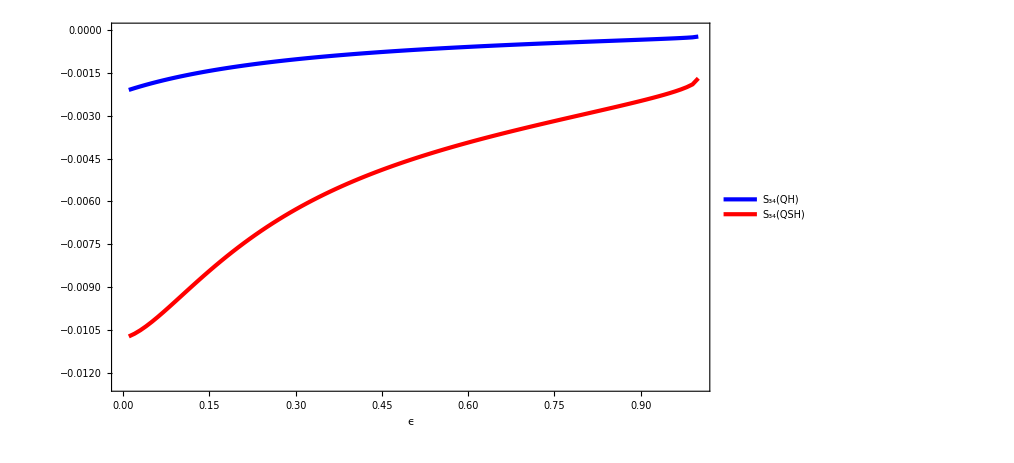

```mathematica
data1=Import["Shot1ad4check.dat"][[All,{1,6}]];
data2=Import["Shot1ad4scheck.dat"][[All,{1,6}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2},Frame->True,PlotRange->{{0,1},{-0.0124,0}},PlotLegends->Placed[{"S_34(QH)","S_34(QSH)"},{Right,Bottom}],ImageSize->750,FrameLabel->{Style["ϵ",35,Black]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Green],Directive[AbsoluteThickness[3],Opacity[1],Black],Directive[AbsoluteThickness[3],Opacity[1],Pink],Directive[AbsoluteThickness[3],Opacity[1],Yellow]},ImageSize->350,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

# Fano-factor for zero-temperature quantum shot noise with voltage probe (Analytical)

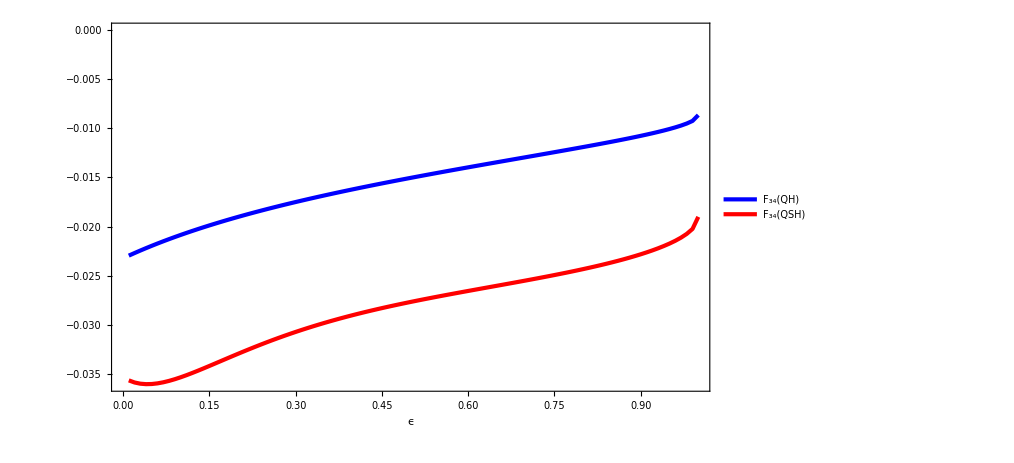

```mathematica
data1=Import["Shot1ad4check.dat"][[All,{1,7}]];
data2=Import["Shot1ad4scheck.dat"][[All,{1,7}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2},Frame->True,PlotRange->All,PlotLegends->Placed[{"F_34(QH)","F_34(QSH)"},{Right,Bottom}],ImageSize->750,FrameLabel->{Style["ϵ",35,Black]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Green],Directive[AbsoluteThickness[3],Opacity[1],Black],Directive[AbsoluteThickness[3],Opacity[1],Pink],Directive[AbsoluteThickness[3],Opacity[1],Yellow]},ImageSize->350,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

# Plot of A_1 and A_2 in QH setup

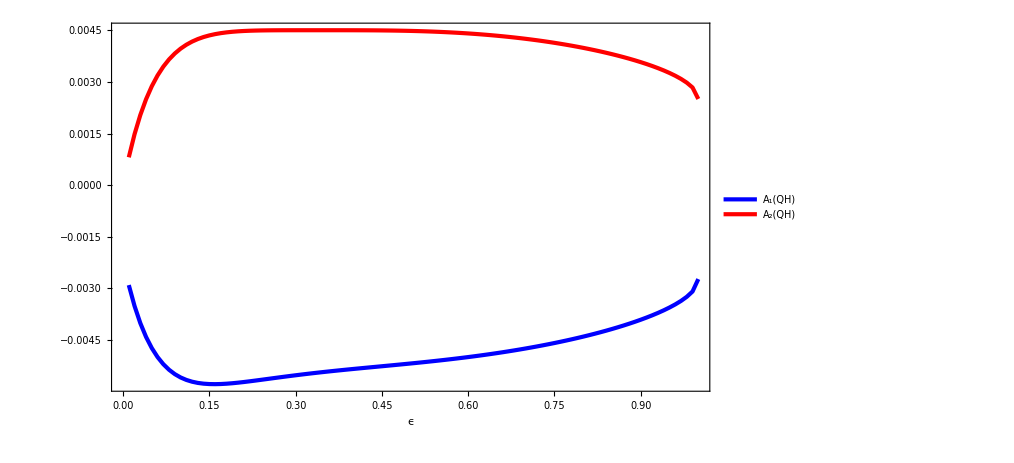

```mathematica
data1=Import["Shot1ad4check.dat"][[All,{1,8}]];
data2=Import["Shot1ad4check.dat"][[All,{1,9}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2},Frame->True,PlotRange->All,PlotLegends->Placed[{"A_1(QH)","A_2(QH)"},{Right,Bottom}],ImageSize->750,FrameLabel->{Style["ϵ",35,Black]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Green],Directive[AbsoluteThickness[3],Opacity[1],Black],Directive[AbsoluteThickness[3],Opacity[1],Pink],Directive[AbsoluteThickness[3],Opacity[1],Yellow]},ImageSize->350,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

# Plot of A_1 and A_2 in QSH setup

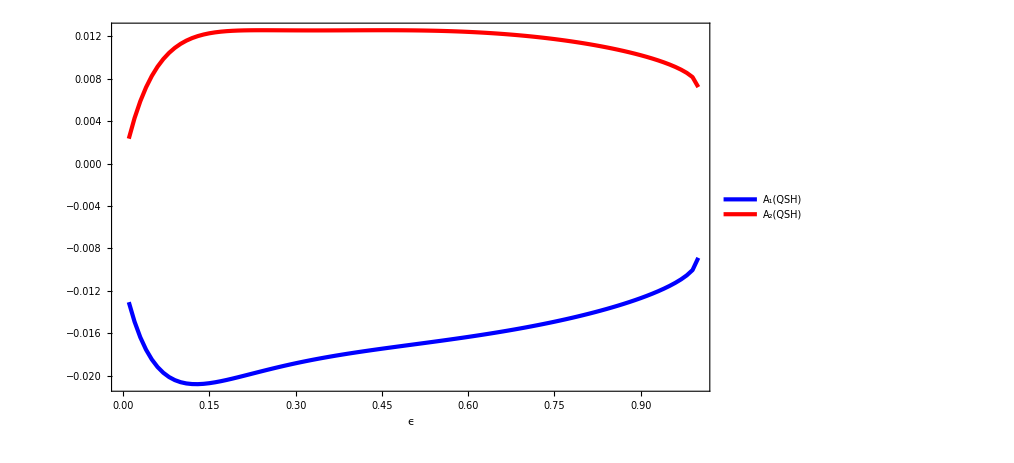

```mathematica
data1=Import["Shot1ad4scheck.dat"][[All,{1,8}]];
data2=Import["Shot1ad4scheck.dat"][[All,{1,9}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2},Frame->True,PlotRange->All,PlotLegends->Placed[{"A_1(QSH)","A_2(QSH)"},{Right,Bottom}],ImageSize->750,FrameLabel->{Style["ϵ",35,Black]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Green],Directive[AbsoluteThickness[3],Opacity[1],Black],Directive[AbsoluteThickness[3],Opacity[1],Pink],Directive[AbsoluteThickness[3],Opacity[1],Yellow]},ImageSize->350,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

# Δ_T noise with voltage-temperature probe (Analytical)

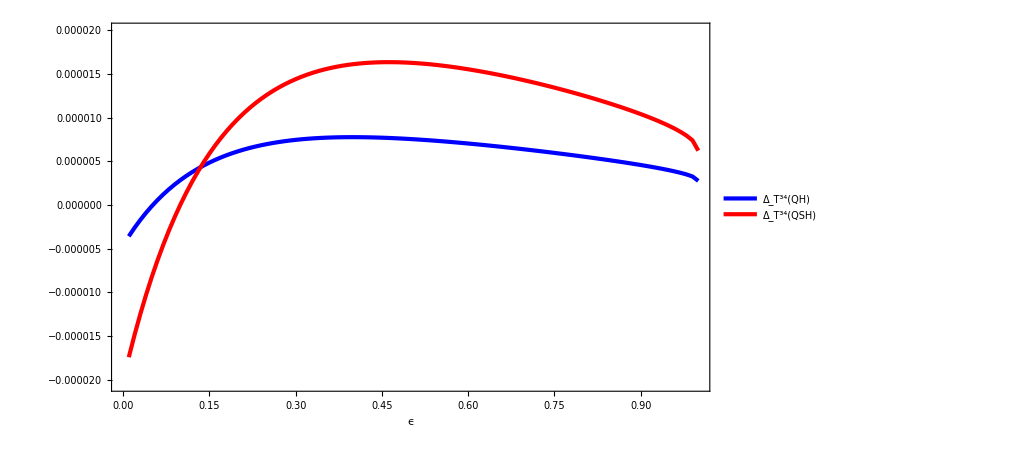

```mathematica
data1=Import["Shot1adQHcheck.dat"][[All,{1,6}]];
data2=Import["Shot1adQSHcheck.dat"][[All,{1,6}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2},Frame->True,PlotRange->{{0,1},{-0.0000205,0.00002}},PlotLegends->Placed[{"Δ_T^34(QH)","Δ_T^34(QSH)"},{Left,Top}],ImageSize->750,FrameLabel->{Style["ϵ",35,Black]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Green],Directive[AbsoluteThickness[3],Opacity[1],Black],Directive[AbsoluteThickness[3],Opacity[1],Pink],Directive[AbsoluteThickness[3],Opacity[1],Yellow]},ImageSize->350,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

# Fano-factor with voltage-temperature probe (Analytical)

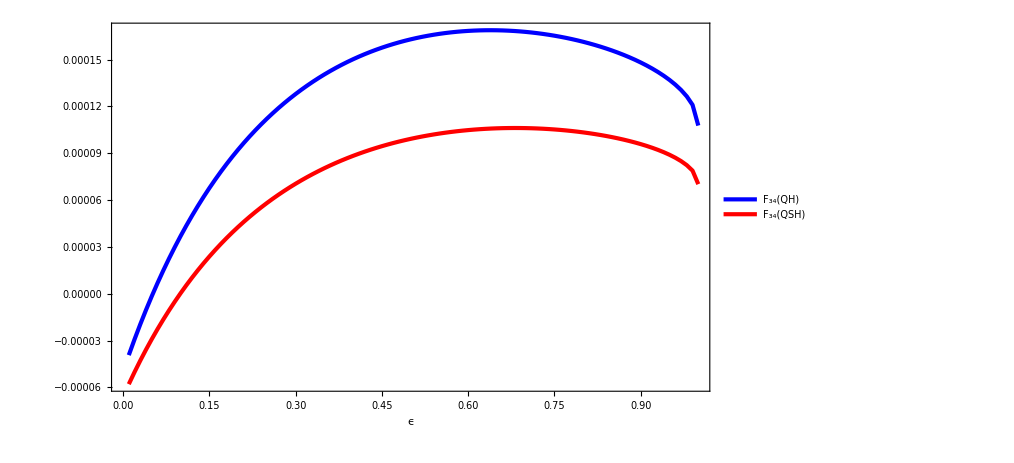

```mathematica
data1=Import["Shot1adQHcheck.dat"][[All,{1,7}]];
data2=Import["Shot1adQSHcheck.dat"][[All,{1,7}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2},Frame->True,PlotRange->All,PlotLegends->Placed[{"F_34(QH)","F_34(QSH)"},{Right,Bottom}],ImageSize->750,FrameLabel->{Style["ϵ",35,Black]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Green],Directive[AbsoluteThickness[3],Opacity[1],Black],Directive[AbsoluteThickness[3],Opacity[1],Pink],Directive[AbsoluteThickness[3],Opacity[1],Yellow]},ImageSize->350,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

# Plot of C_1 and C_2 in QH setup

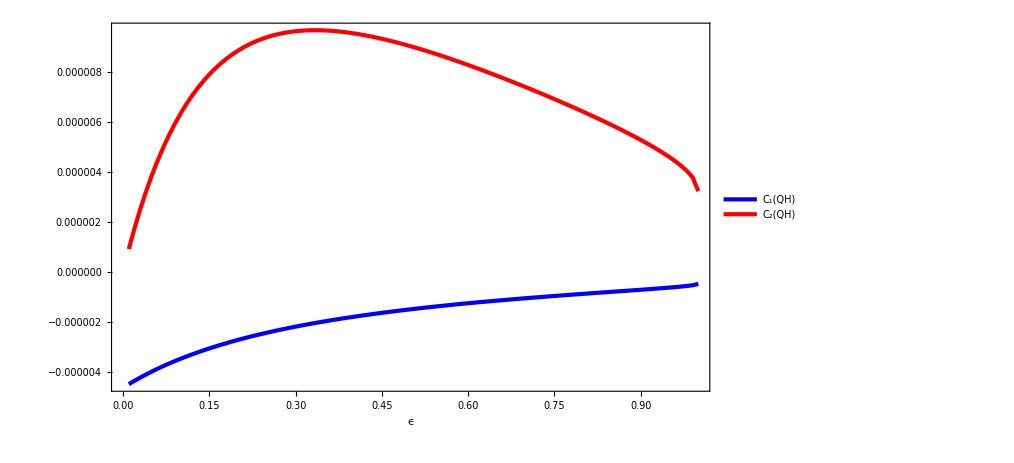

```mathematica
data1=Import["Shot1adQHcheck.dat"][[All,{1,8}]];
data2=Import["Shot1adQHcheck.dat"][[All,{1,9}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2},Frame->True,PlotRange->All,PlotLegends->Placed[{"C_1(QH)","C_2(QH)"},{Right,Bottom}],ImageSize->750,FrameLabel->{Style["ϵ",35,Black]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Green],Directive[AbsoluteThickness[3],Opacity[1],Black],Directive[AbsoluteThickness[3],Opacity[1],Pink],Directive[AbsoluteThickness[3],Opacity[1],Yellow]},ImageSize->350,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

# Plot of C_1 and C_2 in QSH setup

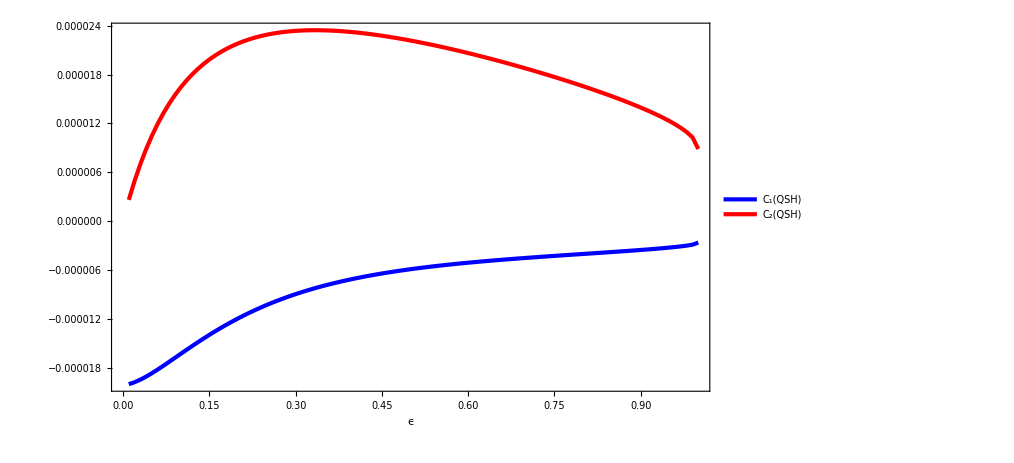

```mathematica
data1=Import["Shot1adQSHcheck.dat"][[All,{1,8}]];
data2=Import["Shot1adQSHcheck.dat"][[All,{1,9}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2},Frame->True,PlotRange->All,PlotLegends->Placed[{"C_1(QSH)","C_2(QSH)"},{Right,Bottom}],ImageSize->750,FrameLabel->{Style["ϵ",35,Black]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Green],Directive[AbsoluteThickness[3],Opacity[1],Black],Directive[AbsoluteThickness[3],Opacity[1],Pink],Directive[AbsoluteThickness[3],Opacity[1],Yellow]},ImageSize->350,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

# Δ_T noise with voltage probe (Analytical)

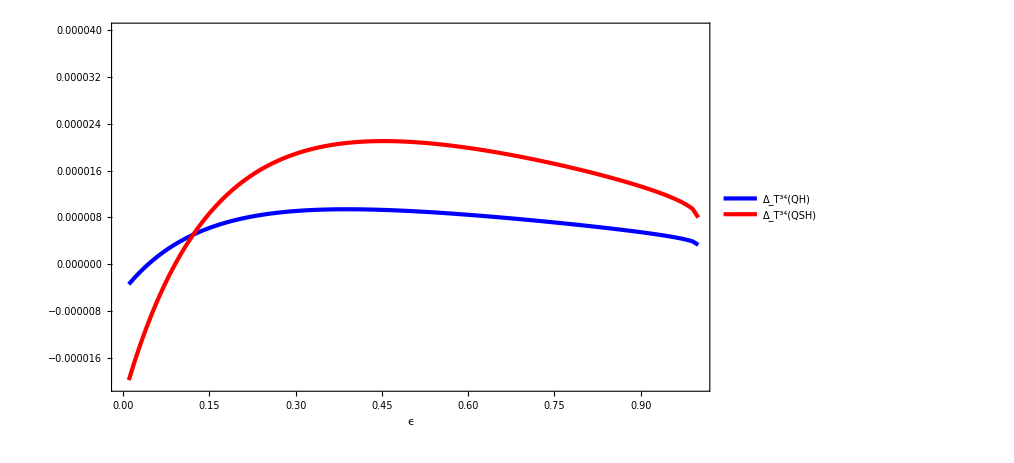

```mathematica
data1=Import["Shot1ad5check.dat"][[All,{1,6}]];
data2=Import["Shot1ad5scheck.dat"][[All,{1,6}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2},Frame->True,PlotRange->{{0,1},{-0.0000205,0.00004}},PlotLegends->Placed[{"Δ_T^34(QH)","Δ_T^34(QSH)"},{Left,Top}],ImageSize->750,FrameLabel->{Style["ϵ",35,Black]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Green],Directive[AbsoluteThickness[3],Opacity[1],Black],Directive[AbsoluteThickness[3],Opacity[1],Pink],Directive[AbsoluteThickness[3],Opacity[1],Yellow]},ImageSize->350,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

# Fano factor with voltage probe (Analytical)

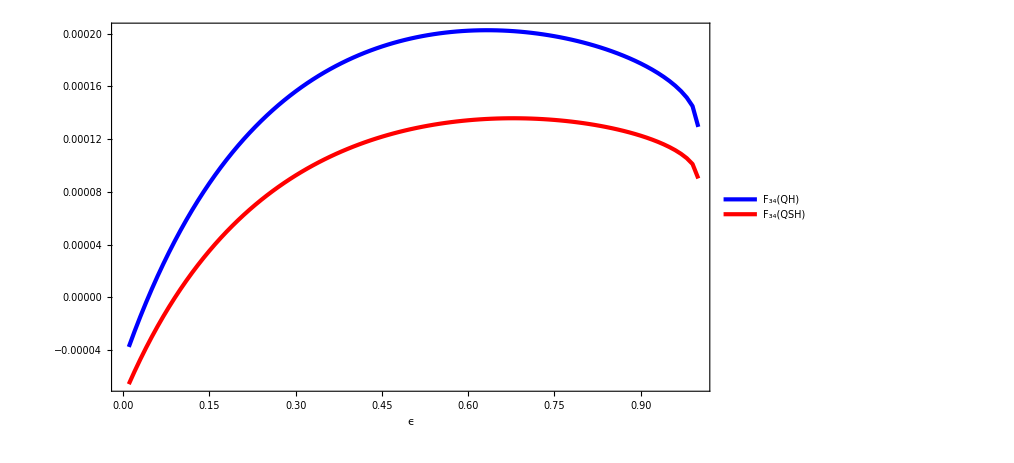

```mathematica
data1=Import["Shot1ad5check.dat"][[All,{1,7}]];
data2=Import["Shot1ad5scheck.dat"][[All,{1,7}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2},Frame->True,PlotRange->All,PlotLegends->Placed[{"F_34(QH)","F_34(QSH)"},{Right,Bottom}],ImageSize->750,FrameLabel->{Style["ϵ",35,Black]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Green],Directive[AbsoluteThickness[3],Opacity[1],Black],Directive[AbsoluteThickness[3],Opacity[1],Pink],Directive[AbsoluteThickness[3],Opacity[1],Yellow]},ImageSize->350,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

# Plot of B_1 and B_2 in QH setup

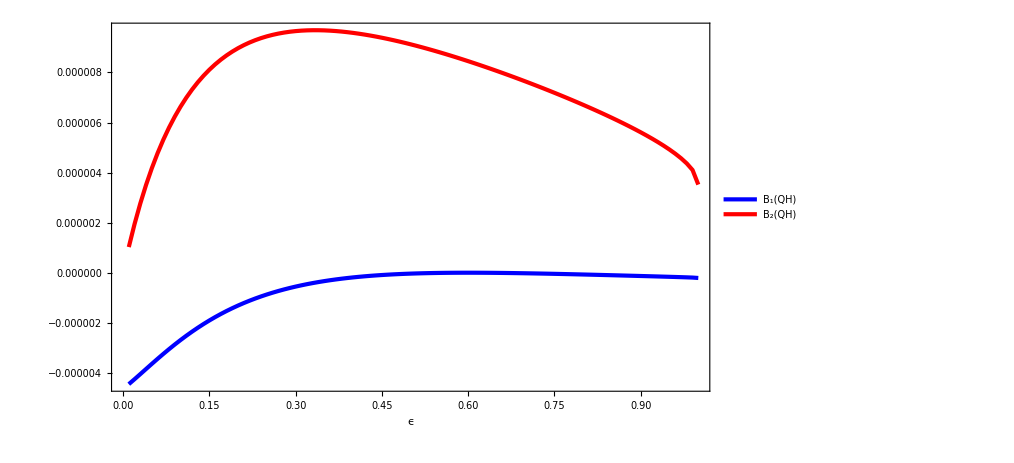

```mathematica
data1=Import["Shot1ad5check.dat"][[All,{1,8}]];
data2=Import["Shot1ad5check.dat"][[All,{1,9}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2},Frame->True,PlotRange->All,PlotLegends->Placed[{"B_1(QH)","B_2(QH)"},{Right,Bottom}],ImageSize->750,FrameLabel->{Style["ϵ",35,Black]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Green],Directive[AbsoluteThickness[3],Opacity[1],Black],Directive[AbsoluteThickness[3],Opacity[1],Pink],Directive[AbsoluteThickness[3],Opacity[1],Yellow]},ImageSize->350,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

# Plot of B_1 and B_2 in QSH setup

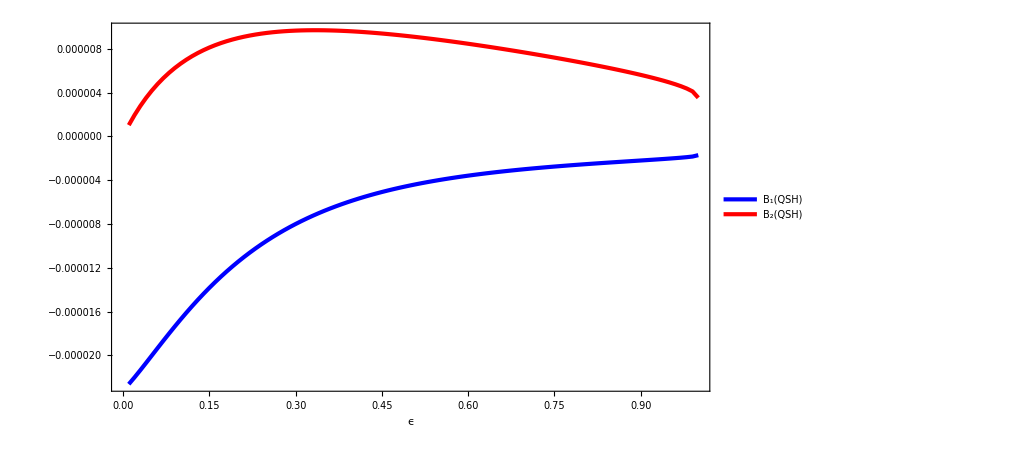

```mathematica
data1=Import["Shot1ad5scheck.dat"][[All,{1,8}]];
data2=Import["Shot1ad5check.dat"][[All,{1,9}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1,data2},Frame->True,PlotRange->All,PlotLegends->Placed[{"B_1(QSH)","B_2(QSH)"},{Right,Bottom}],ImageSize->750,FrameLabel->{Style["ϵ",35,Black]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Green],Directive[AbsoluteThickness[3],Opacity[1],Black],Directive[AbsoluteThickness[3],Opacity[1],Pink],Directive[AbsoluteThickness[3],Opacity[1],Yellow]},ImageSize->350,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

# Spin Fano factor with quantum shot noise

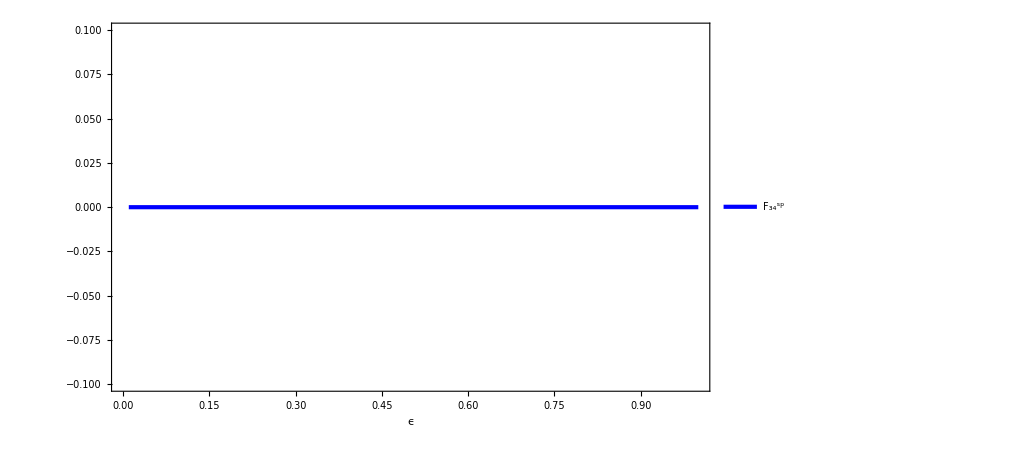

```mathematica
data1=Import["Shot1ad4scheck.dat"][[All,{1,10}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1},Frame->True,PlotRange->{-0.1,0.1},PlotLegends->Placed[{"F_34^sp","F_34(QSH)"},{Right,Bottom}],ImageSize->750,FrameLabel->{Style["ϵ",35,Black]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Green],Directive[AbsoluteThickness[3],Opacity[1],Black],Directive[AbsoluteThickness[3],Opacity[1],Pink],Directive[AbsoluteThickness[3],Opacity[1],Yellow]},ImageSize->350,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

# Spin Fano factor with Δ_T noise with VTP

```mathematica
data1=Import["Shot1adQSHcheck.dat"][[All,{1,10}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1},Frame->True,PlotRange->{-0.1,0.1},PlotLegends->Placed[{"F_34^sp","F_34(QSH)"},{Right,Bottom}],ImageSize->750,FrameLabel->{Style["ϵ",35,Black]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Green],Directive[AbsoluteThickness[3],Opacity[1],Black],Directive[AbsoluteThickness[3],Opacity[1],Pink],Directive[AbsoluteThickness[3],Opacity[1],Yellow]},ImageSize->350,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

-Graphics-

# Spin Fano factor with Δ_T noise with VP

```mathematica
data1=Import["Shot1ad5scheck.dat"][[All,{1,10}]];
Needs["PlotLegends`"]
A1=ListLinePlot[{data1},Frame->True,PlotRange->{-0.1,0.1},PlotLegends->Placed[{"F_34^sp","F_34(QSH)"},{Right,Bottom}],ImageSize->750,FrameLabel->{Style["ϵ",35,Black]},FrameTicksStyle->Directive["Label",Black,25],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Red],Directive[AbsoluteThickness[3],Opacity[1],Green],Directive[AbsoluteThickness[3],Opacity[1],Black],Directive[AbsoluteThickness[3],Opacity[1],Pink],Directive[AbsoluteThickness[3],Opacity[1],Yellow]},ImageSize->350,LabelStyle->Directive[Black,25],FrameStyle->Directive[Black,Thick]]
```

-Graphics-